```mathematica
Quit[];
```

TODO:

# Intro

83-73 = col13int17, col13int18, col14int17, col14int18, col34int13 (tadpole)
              col1313int1, col1313int3, col1414int1, col1414int3, col3434int1  (redundancy)

```mathematica
ReplBetaTheta={beta-> 0.4,theta->0.5};
(*ReplBetaTheta={beta-> 0.000001,theta-> 0.0};*)
```

```mathematica
ReplRemoveTadpole={};
(*ReplRemoveTadpole={col13int17-> 0,col13int18-> 0,col14int17-> 0,col14int18-> 0,col34int13-> 0};*)
```

```mathematica
MyCoefficient[expr_,nap_,nep_]:=Coefficient[Coefficient[expr,ap,nap],ep,nep]
MyFormat=TraditionalForm[#/.Power[expr_,r_?Negative]:>Superscript[expr,r]/.{0.-> 0}]&;
```

Fourier Transform

```mathematica
<<../vp-terms/FourierTransform.m
ReplFT={Log[ⅇ^(-EulerGamma+Lp/2)/mu]->-EulerGamma+Lp/2-Log[mu],PolyGamma[0,1/2]-> -EulerGamma-2Log[2] };
prefacFT=Collect[Normal[Series[qTpFT[Lp,2+2ap+2ep],{ap,0,1},{ep,0,3}]]//.ReplFT,{ap,ep},Simplify];
Coefficient[prefacFT,ep,-1]/.ap-> 0
Coefficient[prefacFT,ep,0]/.ap-> 0
Collect[Coefficient[prefacFT,ep,1]/.ap-> 0,Lp,Simplify]
Coefficient[prefacFT,ep,2]/.ap-> 0
```

-1/4

EulerGamma/4-Lp/2-Log[2]/4+Log[mu]

-Lp^2/2+1/2 Lp (EulerGamma-Log[2]+4 Log[mu])+1/16 (-2 EulerGamma^2-π^2-2 Log[2]^2+EulerGamma Log[16]-16 (EulerGamma-Log[2]) Log[mu]-32 Log[mu]^2)

EulerGamma^3/24-(EulerGamma^2 Lp)/4+(EulerGamma Lp^2)/2-Lp^3/3+(EulerGamma π^2)/16-(Lp π^2)/8-1/8 EulerGamma^2 Log[2]+1/2 EulerGamma Lp Log[2]-1/2 Lp^2 Log[2]+1/8 EulerGamma Log[2]^2-1/4 Lp Log[2]^2-Log[2]^3/24-1/48 π^2 Log[8]+1/2 EulerGamma^2 Log[mu]-2 EulerGamma Lp Log[mu]+2 Lp^2 Log[mu]+1/4 π^2 Log[mu]-EulerGamma Log[2] Log[mu]+2 Lp Log[2] Log[mu]+1/2 Log[2]^2 Log[mu]+2 EulerGamma Log[mu]^2-4 Lp Log[mu]^2-2 Log[2] Log[mu]^2+(8 Log[mu]^3)/3-1/3 PolyGamma[2,1/2]+65/24 PolyGamma[2,1]

```mathematica
NtoM=(2*E^(2*ep*EulerGamma)*(E^(-EulerGamma+Lp/2))^(2*(ap+2*ep))*Sqrt[Pi]*Gamma[-ap-2*ep]*Gamma[1-ep]^2)/(Gamma[1-2*ep]*Gamma[1/2-ep]*Gamma[1+ap+ep])/.Lp-> 0//FullSimplify
```

(2^(1+2 ep) ⅇ^(-2 (ap+ep) EulerGamma) π Gamma[-ap-2 ep] Gamma[1-ep])/(Gamma[1/2-ep]^2 Gamma[1+ap+ep])

```mathematica
NtoMseries=Series[NtoM,{ap,0,2},{ep,0,3}]//Normal//N
```

1.38629-1./ep+0.684028 ep-0.233587 ep^2+1.64009 ep^3+ap^2 (-1.79961-0.25/ep^3+0.346574/ep^2+0.993474/ep-1.75459 ep-15.5965 ep^2-25.0637 ep^3)+ap (-1.98695+0.5/ep^2-0.693147/ep-3.61313 ep+1.0609 ep^2-3.72127 ep^3)

Read all ingredients: bubble, 2cut, 1cut

```mathematica
<<resbubble.m
<<resbubblegg.m
<<resquark.m
<<resquarkgg.m
<<restadpole.m
<<restadpolegg.m
<<bubble-master.m
<<bubble-mastergg.m
<<"1cut/dev-num/1CResultsBd.m"
<<"1cut/dev-num/1CResultsOut.m"
tadpoles2c=<<tadpoles.dat;
(*form2c=<<"2c-nonbub-qq.dat";*)
(*form2c=<<"2c-qq-nonbub-notapole-noabelianredundancy.dat";*)
form2c=<<"2c-qq-nonbub-notapole-noabelianredundancy-no1234redundancy.dat";
form2cgg=<<"2c-gg-nonbub-notapole-noabelianredundancy-no1234redundancy.dat";
Repl2cutBoundaryAbelianF=<<"runs-sfcalc/boundary-abelian/replacements.m";
Repl2cutBoundaryNonAbelianF=<<"runs-sfcalc/boundary-nonabelian/replacements.m";
Repl2cutOutsideF=<<"runs-sfcalc/final-2cut/replacements2cut.m";
(*Repl2cutOutsideF=<<"replacements04Pi4.m";*)
(*Repl2cutOutsideF=<<"runs-sfcalc/replacements04Pi4.m";*)
(*Repl2cutOutsideF=<<"runs-sfcalc/outside/replacements.m";*)
Repl2cutAlphaPolesF=<<"runs-sfcalc/ap12ep1/replacements.m";
Repl2cutep1F=<<"runs-sfcalc/outside-ep1intM/replacements.m";
Repl2cutErrorsF=<<"runs-sfcalc/outside/errors.m";
ReplNames = {col[arg1_][args2__][arg3_]:>  ToExpression[ToString[arg1]<>"int"<>ToString[arg3]]};
(*ReplNames = {col[arg1_][arg2_]:>  ToExpression["col"<>ToString[arg1]<>"int"<>ToString[arg2]]};*)
(*Repl2cutBoundaryAbelian=Repl2cutBoundaryAbelianF;
Repl2cutBoundaryNonAbelian=Repl2cutBoundaryNonAbelianF;
Repl2cutOutside=Repl2cutOutsideF;
Repl2cutAlphaPoles=Repl2cutAlphaPolesF;
Repl2cutErrors=Repl2cutErrorsF;*)
Repl2cutBoundaryAbelian=Repl2cutBoundaryAbelianF/.ReplNames;
Repl2cutBoundaryNonAbelian=Repl2cutBoundaryNonAbelianF/.ReplNames;
Repl2cutOutside=Repl2cutOutsideF/.ReplNames;
Repl2cutAlphaPoles=Repl2cutAlphaPolesF/.ReplNames;
Repl2cutep1=Repl2cutep1F/.ReplNames;
Repl2cutErrors=Repl2cutErrorsF/.ReplNames;
<<"common/ResultsRGE.m"
```

Check that tadpole diagrams are replaced correctly by the analytic formulae

```mathematica
postad= restadpole/.{mu-> 1,Lp-> 0,ap-> 0}/.ReplBetaTheta//N;
Coefficient[postad,ep,-3]
Collect[Coefficient[postad,ep,-2],Nc]
Collect[Coefficient[postad,ep,-1],Nc]
```

{{0,0},{0,0}}

{{2.45716 Nc-2.45716 Nc^3,-1.46649+1.46649 Nc^2},{-1.46649+1.46649 Nc^2,0.852195/Nc-1.19739 Nc+0.345197 Nc^3}}

{{4.98348 Nc-4.98348 Nc^3,-2.93297+2.93297 Nc^2},{-2.93297+2.93297 Nc^2,1.6871/Nc-2.33418 Nc+0.647083 Nc^3}}

```mathematica
pos2cut=prefacFT tadpoles2c/.Repl2cutOutside/.{Lp-> 0,mu-> 1}//Simplify;
(*pos2cut=prefacFT tadpoles2c/.Repl2cutBoundaryNonAbelian/.{Lp-> 0,mu-> 1}//Simplify;*)
MyCoefficient[pos2cut,0,-3]//Simplify
Collect[MyCoefficient[pos2cut,0,-2],Nc]
Collect[MyCoefficient[pos2cut,0,-1],Nc]
```

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0

0

0

Check that we get 73 integrals as we should

```mathematica
integrals=Cases[Expand[Flatten[form2c]],colfac_ Nc^(n_.),-1]/.Nc-> 1//.Times[Rational[a_,b_],colfac_]-> colfac/.Times[-1|2,colfac_]-> colfac//DeleteDuplicates
integrals//Length
```

{col1313int2,col1314int1,col1314int2,col1314int3,col1314int4,col13int19,col13int20,col1414int2,col14int19,col14int20,col3333int1,col3333int2,col3334int1,col34int14,col33int1,col33int2,col34int1,col34int10,col34int11,col34int3,col34int4,col34int5,col34int6,col1333int1,col1333int3,col1333int4,col1334int1,col1334int2,col1433int1,col1433int2,col1433int4,col1434int1,col1434int2,col13int11,col13int12,col13int13,col13int14,col13int15,col13int16,col13int3,col13int4,col14int11,col14int12,col14int13,col14int14,col14int15,col14int16,col14int3,col14int4,col1333int2,col13int1,col13int5,col13int7,col13int9}

54

# Combination outside

Alpha poles for ep^1 terms

```mathematica
Collect[Coefficient[Coefficient[form2c/.Repl2cutAlphaPoles,ep,-5]//Simplify,ap,-2],Nc]
Collect[Coefficient[Coefficient[form2c/.Repl2cutAlphaPoles,ep,-5]//Simplify,ap,-1],Nc]
```

{{0,0},{0,0}}

{{0,0},{0,0}}

```mathematica
posbub=resbubble/.{mu-> 1,Lp-> 0}/.ReplBetaTheta//N;
postad=restadpole/.{mu-> 1,Lp-> 0}/.ReplBetaTheta//N;
posbubep2=Coefficient[posbub,ep,-2];
postadep2=Coefficient[postad,ep,-2];
posbubep1=Collect[Coefficient[posbub,ep,-1],Nc];
postadep1=Collect[Coefficient[postad,ep,-1],Nc];
```

```mathematica
ReplExtra={col33int1-> 0};
res2cut=form2c/.ReplRemoveTadpole/.Repl2cutOutside/.ReplExtra//Simplify;
res2cutSupl=form2c/.ReplRemoveTadpole/.Repl2cutep1/.ReplExtra//Simplify;
err2cut=form2c/.ReplRemoveTadpole/.Repl2cutErrors/.ReplExtra//Simplify;
Collect[res2cut,{ap,ep}]/.Nc-> 3//MatrixForm
```

(314.232+(-25.9883-7.99985/ep^2-1.78643/ep-108.512 ep)/ap+4.00035/ep^3-35.0957/ep^2+11.6386/ep+176.9 ep+(22.1796+15.9995/ep+68.0059 ep)/ap^2 | 82.3346+(-10.7996-7.33312/ep^2+9.67368/ep-45.1611 ep)/ap+6.66646/ep^3-5.90899/ep^2+37.9481/ep-9.81342 ep+(14.7864+10.6663/ep+45.3372 ep)/ap^2
82.3346+(-10.7996-7.33312/ep^2+9.67368/ep-45.1611 ep)/ap+6.66646/ep^3-5.90899/ep^2+37.9481/ep-9.81342 ep+(14.7864+10.6663/ep+45.3372 ep)/ap^2 | -22.0895+(-25.7103-8.66641/ep^2-3.93524/ep-117.876 ep)/ap+6.33304/ep^3-11.926/ep^2+22.0106/ep-122.247 ep+(25.8762+18.6661/ep+79.3402 ep)/ap^2)

```mathematica
pos2cutSupl=prefacFT res2cutSupl/.{Lp-> 0,mu-> 1}//Simplify;
pos2cut=NtoMseries res2cut/.{Lp-> 0,mu-> 1}//Simplify;
pos2cut = pos2cut(* + pos2cutSupl*);
unc2cut=prefacFT err2cut/.{Lp-> 0,mu-> 1}//Simplify;
pos2cutep4 =MyCoefficient[pos2cut,0,-4]//Simplify;
pos2cutep4//MatrixForm
```

(4.50006/Nc-4.50006 Nc | 6.62502-4.50006/Nc^2-2.12496 Nc^2
6.62502-4.50006/Nc^2-2.12496 Nc^2 | 3.37504/Nc^3-5.87492/Nc+3.37483 Nc-0.874961 Nc^3)

```mathematica
pos2cutep3 =MyCoefficient[pos2cut,0,-3]//Simplify;
pos2cutep2 =MyCoefficient[pos2cut,0,-2]//Simplify;
pos2cutep1 =MyCoefficient[pos2cut,0,-1]//Simplify;
pos2cutep0 =MyCoefficient[pos2cut,0,0]//Simplify;
pos2cutep3//MatrixForm
pos2cutep2//MatrixForm
pos2cutep1//MatrixForm
pos2cutep0//MatrixForm
```

(-3.48906/Nc+1.98951 Nc+1.49955 Nc^3 | -9.17226+5.4346/Nc^2+3.73766 Nc^2
-9.17226+5.4346/Nc^2+3.73766 Nc^2 | -4.56233/Nc^3+7.56829/Nc-4.31468 Nc+1.30872 Nc^3)

(9.44687/Nc-8.54505 Nc-0.901818 Nc^3 | 7.68984-3.01404/Nc^2-4.6758 Nc^2
7.68984-3.01404/Nc^2-4.6758 Nc^2 | 0.652324/Nc^3-6.21836/Nc+6.98652 Nc-1.42048 Nc^3)

(-2.11248/Nc+15.2645 Nc-13.1521 Nc^3 | -2.66422+5.99099/Nc^2-3.32677 Nc^2
-2.66422+5.99099/Nc^2-3.32677 Nc^2 | -5.46287/Nc^3-0.511533/Nc+4.18094 Nc+1.79346 Nc^3)

(-127.987/Nc+125.298 Nc+2.68894 Nc^3 | -157.793+122.667/Nc^2+35.126 Nc^2
-157.793+122.667/Nc^2+35.126 Nc^2 | -90.6699/Nc^3+148.759/Nc-74.1397 Nc+16.0505 Nc^3)

```mathematica
pos1cutep3=ICutOutep3;
pos1cutep2=ICutOutep2;
pos1cutep1=ICutOutep1;
pos1cutep3//MatrixForm
pos1cutep2//MatrixForm
pos1cutep1//MatrixForm
```

(0.-0.457164 Nc+0.457164 Nc^3 | 1.46649-1.46649 Nc^2
1.46649-1.46649 Nc^2 | -1.35219/Nc+2.19739 Nc-0.845197 Nc^3)

(0.+0.379014 Nc-0.379014 Nc^3 | 2.48158×10^-7-2.48158×10^-7 Nc^2
2.48158×10^-7-2.48158×10^-7 Nc^2 | -0.0947536/Nc+0.416759 Nc-0.322006 Nc^3)

(0.-1.8361 Nc+1.8361 Nc^3 | -2.41224+2.41224 Nc^2
-2.41224+2.41224 Nc^2 | 2.87127/Nc-4.9052 Nc+2.03393 Nc^3)

```mathematica
(*pos1cutall={{(0.4924122889181345*Nc-0.4924122889181345*Nc^3)/ep^2+(-0.45716374472960153*Nc+0.45716374472960153*Nc^3)/ep^3,(1.1630775156205657-1.1630775156205657*Nc^2)/ep^3+(7.031731365625404*^-6-7.031731365625404*^-6*Nc^2)/ep^2},{(1.1630775156205657-1.1630775156205657*Nc^2)/ep^3+(7.031731365625404*^-6-7.031731365625404*^-6*Nc^2)/ep^2,(-1.0487865794381652/Nc+1.7940699389812191*Nc-0.7452833595430538*Nc^3)/ep^3+(-0.12311010396089994/Nc+0.4434918087799149*Nc-0.32038170481901496*Nc^3)/ep^2}};
pos1cutep3=Coefficient[pos1cutall,ep,-3];
pos1cutep2=Coefficient[pos1cutall,ep,-2]
pos1cutep1=Coefficient[pos1cutall,ep,-1]*)
```

```mathematica
pos1cutep2/.Nc-> 3
```

{{-9.09632,-1.98527×10^-6},{-1.98527×10^-6,-7.47546}}

```mathematica
pos1cutep3
pos2cutep3
```

{{0.-0.457164 Nc+0.457164 Nc^3,1.46649-1.46649 Nc^2},{1.46649-1.46649 Nc^2,-1.35219/Nc+2.19739 Nc-0.845197 Nc^3}}

{{-3.48906/Nc+1.98951 Nc+1.49955 Nc^3,-9.17226+5.4346/Nc^2+3.73766 Nc^2},{-9.17226+5.4346/Nc^2+3.73766 Nc^2,-4.56233/Nc^3+7.56829/Nc-4.31468 Nc+1.30872 Nc^3}}

### ep3

```mathematica
sum3=pos1cutep3+pos2cutep3//MatrixForm
```

(0.-3.48906/Nc+1.53235 Nc+1.95671 Nc^3 | -7.70577+5.4346/Nc^2+2.27117 Nc^2
-7.70577+5.4346/Nc^2+2.27117 Nc^2 | -4.56233/Nc^3+6.2161/Nc-2.11728 Nc+0.46352 Nc^3)

```mathematica
sum3/.Nc-> 3
```

(56.2652 | 13.3386
13.3386 | 8.06623)

### ep2

```mathematica
resep2out =Collect[pos2cutep2+pos1cutep2+posbubep2+postadep2,Nc];
resep2out//MatrixForm
```

(0.+9.44687/Nc-5.32791 Nc-4.11896 Nc^3 | 5.00128-3.01404/Nc^2-1.98724 Nc^2
5.00128-3.01404/Nc^2-1.98724 Nc^2 | 0.652324/Nc^3-4.33409/Nc+4.37473 Nc-0.692962 Nc^3)

```mathematica
Collect[resReep2out/.ReplBetaTheta,Nc]
```

{{4.19666/Nc-4.9303 Nc+0.733634 Nc^3,8.46302-3.63074/Nc^2-4.83228 Nc^2},{8.46302-3.63074/Nc^2-4.83228 Nc^2,2.58157/Nc^3-8.55679/Nc+8.95346 Nc-2.97824 Nc^3}}

```mathematica
diff=(resep2out+resReep2out)/.{a2-> 1,a3-> 1,mk0-> 1(*,Nc-> 3*)}/.ReplBetaTheta//Simplify
```

{{0.+13.6435/Nc-10.2582 Nc-3.38533 Nc^3,13.4643-6.64478/Nc^2-6.81953 Nc^2},{13.4643-6.64478/Nc^2-6.81953 Nc^2,3.2339/Nc^3-12.8909/Nc+13.3282 Nc-3.6712 Nc^3}}

```mathematica
diff/.Nc-> 3
```

{{-117.631,-48.6497},{-48.6497,-63.3151}}

```mathematica
Collect[MyCoefficient[unc2cut,0,-2],Nc]
```

{{0,0},{0,0}}

```mathematica
ReplNc={Nc-> Subscript[N, c]};
Export["ep4matrix.png",MatrixForm[NumberForm[pos2cutep4/.ReplNc//MyFormat,1]]//TraditionalForm,"PNG",ImageResolution-> 300];
Export["ep3matrix.png",MatrixForm[NumberForm[sum3/.ReplNc//MyFormat,1]]//TraditionalForm,"PNG",ImageResolution-> 300];
Export["ep2matrix.png",MatrixForm[NumberForm[diff/.ReplNc//MyFormat,1]]//TraditionalForm,"PNG",ImageResolution-> 300];
```

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

General::stop: Further output of NumberForm::sigz will be suppressed during this calculation.

### ep1

```mathematica
resep1out =Collect[pos2cutep1+pos1cutep1+posbubep1+postadep1,Nc];
resep1out//MatrixForm
```

(0.-2.11248/Nc+19.114 Nc-17.0016 Nc^3 | -10.535+5.99099/Nc^2+4.54406 Nc^2
-10.535+5.99099/Nc^2+4.54406 Nc^2 | -5.46287/Nc^3+6.39692/Nc-6.86376 Nc+5.92971 Nc^3)

```mathematica
Collect[resReep1out/.ReplBetaTheta/.Lp-> 0,Nc]//MatrixForm
```

(0.0233716/Nc+1.28424 Nc-1.30761 Nc^3 | 3.15809-0.0749711/Nc^2-3.08312 Nc^2
3.15809-0.0749711/Nc^2-3.08312 Nc^2 | 0.0691282/Nc^3-3.49015/Nc+5.27614 Nc-1.85512 Nc^3)

```mathematica
diff=(resep1out+resReep1out)/.ReplBetaTheta/.Lp-> 0(*/.{a1-> 1,a2-> 1,a3-> 1,mk0-> 1}*)//Simplify
```

{{-2.08911/Nc+20.3983 Nc-18.3092 Nc^3,-7.37695+5.91601/Nc^2+1.46093 Nc^2},{-7.37695+5.91601/Nc^2+1.46093 Nc^2,-5.39374/Nc^3+2.90677/Nc-1.58761 Nc+4.07459 Nc^3}}

```mathematica
Collect[MyCoefficient[unc2cut,0,-1],Nc]
```

{{-1/(8 Nc)(-col1313int2+col1314int1+col1314int2+col1314int3+col1314int4+2 col13int19+2 col13int20-col1414int2+2 col14int19+2 col14int20+col3333int1+col3333int2-2 col3334int1-2 col34int14)-1/8 (col1313int2-col1314int1-col1314int2-col1314int3-col1314int4-2 col13int19-2 col13int20+col1414int2-2 col14int19-2 col14int20-2 col3333int1-2 col3333int2+4 col3334int1+col33int2-2 col34int1-2 col34int10-col34int11+3 col34int14-col34int3-2 col34int4-2 col34int5-2 col34int6) Nc-1/8 (col3333int1+col3333int2-2 col3334int1-col33int2+2 col34int1+2 col34int10+col34int11-col34int14+col34int3+2 col34int4+2 col34int5+2 col34int6) Nc^3,1/32 (-5 (col1314int1+col1314int2+col1314int3+col1314int4)-4 (col1333int1+col1333int2+col1333int3+col1333int4)-3 (-col1334int1-col1334int2)+6 (col1313int2-2 (col13int19+col13int20))+2 (2 col13int1+col13int11+col13int12+col13int13+col13int14+col13int15+col13int16+col13int19+col13int20+col13int3+col13int4+2 col13int5+2 col13int7+2 col13int9)+4 (col1333int2+col1433int1+col1433int2+col1433int4)-3 (col1434int1+col1434int2)+4 (col1414int2-2 (col14int19+col14int20))-2 (2 col13int1+2 col13int5+2 col13int7+2 col13int9+col14int11+col14int12+col14int13+col14int14+col14int15+col14int16+col14int19+col14int20+col14int3+col14int4))+1/(32 Nc^2)(4 (col1314int1+col1314int2+col1314int3+col1314int4)+2 (col1333int1+col1333int2+col1333int3+col1333int4)+2 (-col1334int1-col1334int2)-4 (col1313int2-2 (col13int19+col13int20))-2 (col1333int2+col1433int1+col1433int2+col1433int4)+2 (col1434int1+col1434int2)-4 (col1414int2-2 (col14int19+col14int20)))+1/32 (col1314int1+col1314int2+col1314int3+col1314int4+2 (col1333int1+col1333int2+col1333int3+col1333int4)-col1334int1-col1334int2-2 (col1313int2-2 (col13int19+col13int20))-2 (2 col13int1+col13int11+col13int12+col13int13+col13int14+col13int15+col13int16+col13int19+col13int20+col13int3+col13int4+2 col13int5+2 col13int7+2 col13int9)-2 (col1333int2+col1433int1+col1433int2+col1433int4)+col1434int1+col1434int2+2 (2 col13int1+2 col13int5+2 col13int7+2 col13int9+col14int11+col14int12+col14int13+col14int14+col14int15+col14int16+col14int19+col14int20+col14int3+col14int4)) Nc^2},{1/32 (-5 (col1314int1+col1314int2+col1314int3+col1314int4)-4 (col1333int1+col1333int2+col1333int3+col1333int4)-3 (-col1334int1-col1334int2)+6 (col1313int2-2 (col13int19+col13int20))+2 (2 col13int1+col13int11+col13int12+col13int13+col13int14+col13int15+col13int16+col13int19+col13int20+col13int3+col13int4+2 col13int5+2 col13int7+2 col13int9)+4 (col1333int2+col1433int1+col1433int2+col1433int4)-3 (col1434int1+col1434int2)+4 (col1414int2-2 (col14int19+col14int20))-2 (2 col13int1+2 col13int5+2 col13int7+2 col13int9+col14int11+col14int12+col14int13+col14int14+col14int15+col14int16+col14int19+col14int20+col14int3+col14int4))+1/(32 Nc^2)(4 (col1314int1+col1314int2+col1314int3+col1314int4)+2 (col1333int1+col1333int2+col1333int3+col1333int4)+2 (-col1334int1-col1334int2)-4 (col1313int2-2 (col13int19+col13int20))-2 (col1333int2+col1433int1+col1433int2+col1433int4)+2 (col1434int1+col1434int2)-4 (col1414int2-2 (col14int19+col14int20)))+1/32 (col1314int1+col1314int2+col1314int3+col1314int4+2 (col1333int1+col1333int2+col1333int3+col1333int4)-col1334int1-col1334int2-2 (col1313int2-2 (col13int19+col13int20))-2 (2 col13int1+col13int11+col13int12+col13int13+col13int14+col13int15+col13int16+col13int19+col13int20+col13int3+col13int4+2 col13int5+2 col13int7+2 col13int9)-2 (col1333int2+col1433int1+col1433int2+col1433int4)+col1434int1+col1434int2+2 (2 col13int1+2 col13int5+2 col13int7+2 col13int9+col14int11+col14int12+col14int13+col14int14+col14int15+col14int16+col14int19+col14int20+col14int3+col14int4)) Nc^2,-1/(32 Nc^3)(3 (col1314int1+col1314int2+col1314int3+col1314int4)-2 (-col1333int1-col1333int2-col1333int3-col1333int4)+2 (-col1334int1-col1334int2)-3 (col1313int2-2 (col13int19+col13int20))-2 (col1333int2+col1433int1+col1433int2+col1433int4)+2 (col1434int1+col1434int2)-3 (col1414int2-2 (col14int19+col14int20))-col3333int1-col3333int2+2 col3334int1+2 col34int14)-1/(32 Nc)(-4 (col1314int1+col1314int2+col1314int3+col1314int4)+5 (-col1333int1-col1333int2-col1333int3-col1333int4)-3 (-col1334int1-col1334int2)+6 (col1313int2-2 (col13int19+col13int20))+2 (2 col13int1+col13int11+col13int12+col13int13+col13int14+col13int15+col13int16+col13int19+col13int20+col13int3+col13int4+2 col13int5+2 col13int7+2 col13int9)+4 (col1333int2+col1433int1+col1433int2+col1433int4)-2 (col1434int1+col1434int2)+2 (col1414int2-2 (col14int19+col14int20))-2 (2 col13int1+2 col13int5+2 col13int7+2 col13int9+col14int11+col14int12+col14int13+col14int14+col14int15+col14int16+col14int19+col14int20+col14int3+col14int4)+3 (col3333int1+col3333int2)-4 col3334int1-col33int2+2 col34int1+2 col34int10+col34int11-col34int14+col34int3+2 col34int4+2 col34int5+2 col34int6)-1/32 (col1314int1+col1314int2+col1314int3+col1314int4-4 (-col1333int1-col1333int2-col1333int3-col1333int4)-col1334int1-col1334int2-4 (col1313int2-2 (col13int19+col13int20))-3 (2 col13int1+col13int11+col13int12+col13int13+col13int14+col13int15+col13int16+col13int19+col13int20+col13int3+col13int4+2 col13int5+2 col13int7+2 col13int9)+col1414int2-2 (col1333int2+col1433int1+col1433int2+col1433int4)-2 (col14int19+col14int20)+2 (2 col13int1+2 col13int5+2 col13int7+2 col13int9+col14int11+col14int12+col14int13+col14int14+col14int15+col14int16+col14int19+col14int20+col14int3+col14int4)-3 (col3333int1+col3333int2)+2 col3334int1+2 col33int2-2 col34int1-2 col34int10-col34int11-col34int14-col34int3-2 col34int4-2 col34int5-2 col34int6) Nc-1/32 (col1313int2-col1333int1-col1333int2-col1333int3-col1333int4+2 col13int1+col13int11+col13int12+col13int13+col13int14+col13int15+col13int16+col13int19+col13int20-2 (col13int19+col13int20)+col13int3+col13int4+2 col13int5+2 col13int7+2 col13int9+col3333int1+col3333int2-col33int2) Nc^3}}

```mathematica
posbubep1//MatrixForm
postadep1//MatrixForm
```

(0.702133 Nc-0.702133 Nc^3 | -2.52561+2.52561 Nc^2
-2.52561+2.52561 Nc^2 | 2.35008/Nc-3.80531 Nc+1.45523 Nc^3)

(4.98348 Nc-4.98348 Nc^3 | -2.93297+2.93297 Nc^2
-2.93297+2.93297 Nc^2 | 1.6871/Nc-2.33418 Nc+0.647083 Nc^3)

### ep0

```mathematica
resep0out =Collect[pos2cutep0,Nc];
(*resep1out =Collect[pos2cutep1+pos1cutep1+posbubep1+postadep1,Nc];*)
resep0out//MatrixForm
```

(-127.987/Nc+125.298 Nc+2.68894 Nc^3 | -157.793+122.667/Nc^2+35.126 Nc^2
-157.793+122.667/Nc^2+35.126 Nc^2 | -90.6699/Nc^3+148.759/Nc-74.1397 Nc+16.0505 Nc^3)

## Alternative derivation: maximal use of RGE

```mathematica
Replf=Table[f[i,j]-> Coefficient[Coefficient[prefacFT/.{ap-> 0,mu-> 1},ep,i],Lp,j],{i,-1,1},{j,-1,2}]//Flatten
```

{f[-1,-1]→0,f[-1,0]→-1/4,f[-1,1]→0,f[-1,2]→0,f[0,-1]→0,f[0,0]→1/4 (EulerGamma-Log[2]),f[0,1]→-1/2,f[0,2]→0,f[1,-1]→0,f[1,0]→1/16 (-2 EulerGamma^2-π^2+4 EulerGamma Log[2]-2 Log[2]^2),f[1,1]→1/16 (8 EulerGamma-8 Log[2]),f[1,2]→-1/2}

### ep2

```mathematica
s[-1]=-resReep2out/f[-1,0]/.Replf//Simplify
resep2alt=Collect[Coefficient[Coefficient[(f[-1,0]s[-1])/.Replf//Simplify,ep,0],ap,0],Nc]
```

{{-1/(3 beta^2 Nc)2 (-1+Nc^2) (beta (1+beta^2) (-12+23 Nc^2) Log[(1-beta)/(1+beta)]+3 (1+beta^2)^2 (-1+Nc^2) Log[(1-beta)/(1+beta)]^2+2 beta^2 (-6+17 Nc^2+24 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-6 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-24 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])),1/(3 beta Nc^2)2 (-1+Nc^2) (-12 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+2 Log[(1-beta Cos[theta])/(√(1-beta^2))] (3 (1+beta^2) (-2+Nc^2) Log[(1-beta)/(1+beta)]-2 beta (6-17 Nc^2+3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+3 (-4+Nc^2) Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]))+beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-11 Nc^2+6 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-48 Log[(1+beta Cos[theta])/(√(1-beta^2))])+2 (-3 (1+beta^2) (-2+Nc^2) Log[(1-beta)/(1+beta)]+2 beta (6-17 Nc^2+3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)])) Log[(1+beta Cos[theta])/(√(1-beta^2))])},{1/(3 beta Nc^2)2 (-1+Nc^2) (-12 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+2 Log[(1-beta Cos[theta])/(√(1-beta^2))] (3 (1+beta^2) (-2+Nc^2) Log[(1-beta)/(1+beta)]-2 beta (6-17 Nc^2+3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+3 (-4+Nc^2) Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]))+beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-11 Nc^2+6 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-48 Log[(1+beta Cos[theta])/(√(1-beta^2))])+2 (-3 (1+beta^2) (-2+Nc^2) Log[(1-beta)/(1+beta)]+2 beta (6-17 Nc^2+3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)])) Log[(1+beta Cos[theta])/(√(1-beta^2))]),-1/(6 beta^2 Nc^3)(-1+Nc^2) (3 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2+beta (1+beta^2) Log[(1-beta)/(1+beta)] (12-23 Nc^2+24 (-2+Nc^2) Log[(1-beta Cos[theta])/(√(1-beta^2))]+48 Log[(1+beta Cos[theta])/(√(1-beta^2))])+2 beta^2 (6-23 Nc^2+17 Nc^4-6 Nc^4 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]^2-22 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-18 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-6 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+4 Log[(1-beta Cos[theta])/(√(1-beta^2))] (-12+40 Nc^2-17 Nc^4+6 Nc^2 (-2+Nc^2) Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-6 (-3+Nc^2) Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2])+48 Log[(1+beta Cos[theta])/(√(1-beta^2))]-136 Nc^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]-72 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-24 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] (11 Nc^2+24 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+48 Log[(1+beta Cos[theta])/(√(1-beta^2))])))}}

{{(Nc^3 (34 beta^2+23 beta (1+beta^2) Log[(1-beta)/(1+beta)]+3 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2))/(6 beta^2)+1/(6 beta^2)Nc (-46 beta^2-35 beta (1+beta^2) Log[(1-beta)/(1+beta)]-6 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2+48 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-48 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/(6 beta^2 Nc)(12 beta^2+12 beta (1+beta^2) Log[(1-beta)/(1+beta)]+3 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2-48 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+12 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+48 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]),-1/(6 beta)Nc^2 (68 beta Log[(1-beta Cos[theta])/(√(1-beta^2))]+6 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-12 beta Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-11 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 beta Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+6 beta Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-68 beta Log[(1+beta Cos[theta])/(√(1-beta^2))]-6 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+12 beta Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))])-1/(6 beta)(-92 beta Log[(1-beta Cos[theta])/(√(1-beta^2))]-18 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+12 beta Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+11 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+60 beta Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-6 beta Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+92 beta Log[(1+beta Cos[theta])/(√(1-beta^2))]+18 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-12 beta Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-48 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])-1/(6 beta Nc^2)(24 beta Log[(1-beta Cos[theta])/(√(1-beta^2))]+12 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-48 beta Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+12 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-24 beta Log[(1+beta Cos[theta])/(√(1-beta^2))]-12 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+48 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])},{-1/(6 beta)Nc^2 (68 beta Log[(1-beta Cos[theta])/(√(1-beta^2))]+6 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-12 beta Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-11 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 beta Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+6 beta Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-68 beta Log[(1+beta Cos[theta])/(√(1-beta^2))]-6 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+12 beta Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))])-1/(6 beta)(-92 beta Log[(1-beta Cos[theta])/(√(1-beta^2))]-18 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+12 beta Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+11 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+60 beta Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-6 beta Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+92 beta Log[(1+beta Cos[theta])/(√(1-beta^2))]+18 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-12 beta Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-48 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])-1/(6 beta Nc^2)(24 beta Log[(1-beta Cos[theta])/(√(1-beta^2))]+12 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-48 beta Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+12 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-24 beta Log[(1+beta Cos[theta])/(√(1-beta^2))]-12 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+48 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]),1/(24 beta^2)Nc^3 (34 beta^2-136 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]+22 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+48 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-12 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]^2)+1/(24 beta^2 Nc)(58 beta^2+35 beta (1+beta^2) Log[(1-beta)/(1+beta)]+3 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2-416 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]-72 beta (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+96 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+44 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+192 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-48 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-24 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+368 beta^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]+48 beta (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-96 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-96 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/(24 beta^2)Nc (-80 beta^2-23 beta (1+beta^2) Log[(1-beta)/(1+beta)]+456 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]+24 beta (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-22 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-144 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+12 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]^2-44 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-48 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+48 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-272 beta^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]+96 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-48 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/(24 beta^2 Nc^3)(-12 beta^2-12 beta (1+beta^2) Log[(1-beta)/(1+beta)]-3 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2+96 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]+48 beta (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-144 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-96 beta^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]-48 beta (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+144 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])}}

1/ep^2 is exactly determined from RG

```mathematica
resep2alt+resReep2out//Simplify
```

{{0,0},{0,0}}

### ep1

```mathematica
sbub[0]=Coefficient[posbub/(prefacFT/.{ap-> 0,mu-> 1,Lp-> 0}),ep,0]//Simplify
stad[0]=Coefficient[postad/(prefacFT/.{ap-> 0,mu-> 1,Lp-> 0}),ep,0]//Simplify
s1cut[0]=Coefficient[(pos1cutep3/ep^3+pos1cutep2/ep^2+pos1cutep1/ep)/(prefacFT/.{ap-> 0,mu-> 1,Lp-> 0}),ep,0]//Simplify
s2cut[0]=Coefficient[res2cut/.{Lp-> 0,mu-> 1},ep,0]//Simplify
```

{{-2.63187 Nc+2.63187 Nc^3,9.53575-9.53575 Nc^2},{9.53575-9.53575 Nc^2,-8.87779/Nc+14.3721 Nc-5.49431 Nc^3}}

{{-18.7945 Nc+18.7945 Nc^3,11.0518-11.0518 Nc^2},{11.0518-11.0518 Nc^2,-6.35322/Nc+8.78148 Nc-2.42825 Nc^3}}

{{3.02042 Nc-3.02042 Nc^3,24.0832-24.0832 Nc^2},{24.0832-24.0832 Nc^2,-24.8383/Nc+41.4424 Nc-16.6041 Nc^3}}

{{(-8.31735+8.31735 Nc^2+ap (9.74561-9.74561 Nc^2)+ap^2 (-23.3853+12.8906 Nc^2+10.4947 Nc^4))/(ap^2 Nc),(8.31735-11.0898 Nc^2+2.77245 Nc^4+ap (-8.7445+11.0661 Nc^2-2.32157 Nc^4)+ap^2 (4.08048-14.8257 Nc^2+10.7452 Nc^4))/(ap^2 Nc^2)},{(8.31735-11.0898 Nc^2+2.77245 Nc^4+ap (-8.7445+11.0661 Nc^2-2.32157 Nc^4)+ap^2 (4.08048-14.8257 Nc^2+10.7452 Nc^4))/(ap^2 Nc^2),1/(ap^2 Nc^3)(-6.23801+9.70357 Nc^2-4.85179 Nc^4+1.38622 Nc^6+ap (6.30809-11.5877 Nc^2+6.85963 Nc^4-1.58001 Nc^6)+ap^2 (1.76584+15.6253 Nc^2-18.4249 Nc^4+1.03375 Nc^6))}}

```mathematica
s[0]=sbub[0]+stad[0]+s1cut[0]+s2cut[0];
resep1alt=Collect[Coefficient[Coefficient[(f[-1,0]s[0]+f[0,0]s[-1])/.Replf//Simplify,ep,0],ap,0],Nc]
```

{{1/6 Nc^3 (-39.4092-(23 EulerGamma Log[(1-beta)/(1+beta)])/beta-23 beta EulerGamma Log[(1-beta)/(1+beta)]+(23 Log[2] Log[(1-beta)/(1+beta)])/beta+23 beta Log[2] Log[(1-beta)/(1+beta)]-6 EulerGamma Log[(1-beta)/(1+beta)]^2-(3 EulerGamma Log[(1-beta)/(1+beta)]^2)/beta^2-3 beta^2 EulerGamma Log[(1-beta)/(1+beta)]^2+6 Log[2] Log[(1-beta)/(1+beta)]^2+(3 Log[2] Log[(1-beta)/(1+beta)]^2)/beta^2+3 beta^2 Log[2] Log[(1-beta)/(1+beta)]^2)+1/6 Nc (2.94013+(35 EulerGamma Log[(1-beta)/(1+beta)])/beta+35 beta EulerGamma Log[(1-beta)/(1+beta)]-(35 Log[2] Log[(1-beta)/(1+beta)])/beta-35 beta Log[2] Log[(1-beta)/(1+beta)]+12 EulerGamma Log[(1-beta)/(1+beta)]^2+(6 EulerGamma Log[(1-beta)/(1+beta)]^2)/beta^2+6 beta^2 EulerGamma Log[(1-beta)/(1+beta)]^2-12 Log[2] Log[(1-beta)/(1+beta)]^2-(6 Log[2] Log[(1-beta)/(1+beta)]^2)/beta^2-6 beta^2 Log[2] Log[(1-beta)/(1+beta)]^2-48 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+48 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+12 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-12 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+48 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-48 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/(6 Nc)(36.4691-(12 EulerGamma Log[(1-beta)/(1+beta)])/beta-12 beta EulerGamma Log[(1-beta)/(1+beta)]+(12 Log[2] Log[(1-beta)/(1+beta)])/beta+12 beta Log[2] Log[(1-beta)/(1+beta)]-6 EulerGamma Log[(1-beta)/(1+beta)]^2-(3 EulerGamma Log[(1-beta)/(1+beta)]^2)/beta^2-3 beta^2 EulerGamma Log[(1-beta)/(1+beta)]^2+6 Log[2] Log[(1-beta)/(1+beta)]^2+(3 Log[2] Log[(1-beta)/(1+beta)]^2)/beta^2+3 beta^2 Log[2] Log[(1-beta)/(1+beta)]^2+48 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-48 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+12 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-48 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+48 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]),1/6 Nc^2 (50.8883+68 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))]-68 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))]+(6 EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta+6 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-(6 Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta-6 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-12 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+12 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-11 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+11 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+12 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+6 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-6 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-68 EulerGamma Log[(1+beta Cos[theta])/(√(1-beta^2))]+68 Log[2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-(6 EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta-6 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+(6 Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta+6 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+12 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-12 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/(6 Nc^2)(-6.12072+24 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))]-24 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))]+(12 EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta+12 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-(12 Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta-12 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-48 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+48 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+12 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-12 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-24 EulerGamma Log[(1+beta Cos[theta])/(√(1-beta^2))]+24 Log[2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-(12 EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta-12 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+(12 Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta+12 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+48 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-48 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/6 (-44.7676-92 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))]+92 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))]-(18 EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta-18 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+(18 Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta+18 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+12 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-12 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+11 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-11 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+60 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-60 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-6 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+6 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+12 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+92 EulerGamma Log[(1+beta Cos[theta])/(√(1-beta^2))]-92 Log[2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+(18 EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta+18 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-(18 Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta-18 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-12 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+12 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-48 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+48 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])},{1/6 Nc^2 (50.8883+68 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))]-68 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))]+(6 EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta+6 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-(6 Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta-6 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-12 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+12 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-11 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+11 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+12 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+6 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-6 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-68 EulerGamma Log[(1+beta Cos[theta])/(√(1-beta^2))]+68 Log[2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-(6 EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta-6 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+(6 Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta+6 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+12 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-12 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/(6 Nc^2)(-6.12072+24 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))]-24 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))]+(12 EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta+12 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-(12 Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta-12 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-48 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+48 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+12 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-12 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-24 EulerGamma Log[(1+beta Cos[theta])/(√(1-beta^2))]+24 Log[2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-(12 EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta-12 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+(12 Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta+12 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+48 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-48 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/6 (-44.7676-92 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))]+92 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))]-(18 EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta-18 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+(18 Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta+18 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+12 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-12 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+11 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-11 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+60 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-60 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-6 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+6 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-12 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+12 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+92 EulerGamma Log[(1+beta Cos[theta])/(√(1-beta^2))]-92 Log[2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+(18 EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta+18 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-(18 Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta-18 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-12 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+12 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-48 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+48 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]),Nc^3 (6.03746+17/3 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))]-17/3 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))]-11/12 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+11/12 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-2 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+2 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+1/2 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]^2-1/2 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]^2)+1/Nc(6.39116-(35 EulerGamma Log[(1-beta)/(1+beta)])/(24 beta)-35/24 beta EulerGamma Log[(1-beta)/(1+beta)]+(35 Log[2] Log[(1-beta)/(1+beta)])/(24 beta)+35/24 beta Log[2] Log[(1-beta)/(1+beta)]-1/4 EulerGamma Log[(1-beta)/(1+beta)]^2-(EulerGamma Log[(1-beta)/(1+beta)]^2)/(8 beta^2)-1/8 beta^2 EulerGamma Log[(1-beta)/(1+beta)]^2+1/4 Log[2] Log[(1-beta)/(1+beta)]^2+(Log[2] Log[(1-beta)/(1+beta)]^2)/(8 beta^2)+1/8 beta^2 Log[2] Log[(1-beta)/(1+beta)]^2+52/3 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))]-52/3 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))]+(3 EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta+3 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-(3 Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta-3 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-4 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+4 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-11/6 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+11/6 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-8 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+8 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+2 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-2 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-46/3 EulerGamma Log[(1+beta Cos[theta])/(√(1-beta^2))]+46/3 Log[2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-(2 EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta-2 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+(2 Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta+2 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+4 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-4 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+4 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-4 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])+Nc (-11.9292+(23 EulerGamma Log[(1-beta)/(1+beta)])/(24 beta)+23/24 beta EulerGamma Log[(1-beta)/(1+beta)]-(23 Log[2] Log[(1-beta)/(1+beta)])/(24 beta)-23/24 beta Log[2] Log[(1-beta)/(1+beta)]-19 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))]+19 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))]-(EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta-beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+(Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta+beta Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+11/12 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-11/12 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+6 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-6 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-1/2 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]^2+1/2 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]^2+11/6 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-11/6 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+2 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-2 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-2 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+2 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+1/2 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-1/2 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+34/3 EulerGamma Log[(1+beta Cos[theta])/(√(1-beta^2))]-34/3 Log[2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-4 EulerGamma Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+4 Log[2] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+2 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-2 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/Nc^3(-0.499425+(EulerGamma Log[(1-beta)/(1+beta)])/(2 beta)+1/2 beta EulerGamma Log[(1-beta)/(1+beta)]-(Log[2] Log[(1-beta)/(1+beta)])/(2 beta)-1/2 beta Log[2] Log[(1-beta)/(1+beta)]+1/4 EulerGamma Log[(1-beta)/(1+beta)]^2+(EulerGamma Log[(1-beta)/(1+beta)]^2)/(8 beta^2)+1/8 beta^2 EulerGamma Log[(1-beta)/(1+beta)]^2-1/4 Log[2] Log[(1-beta)/(1+beta)]^2-(Log[2] Log[(1-beta)/(1+beta)]^2)/(8 beta^2)-1/8 beta^2 Log[2] Log[(1-beta)/(1+beta)]^2-4 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))]+4 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))]-(2 EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta-2 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+(2 Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))])/beta+2 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+6 EulerGamma Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-6 Log[2] Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-3/2 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+3/2 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+4 EulerGamma Log[(1+beta Cos[theta])/(√(1-beta^2))]-4 Log[2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+(2 EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta+2 beta EulerGamma Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-(2 Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))])/beta-2 beta Log[2] Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-6 EulerGamma Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+6 Log[2] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])}}

```mathematica
resep1out
```

{{0.-2.11248/Nc+19.114 Nc-17.0016 Nc^3,-10.535+5.99099/Nc^2+4.54406 Nc^2},{-10.535+5.99099/Nc^2+4.54406 Nc^2,-5.46287/Nc^3+6.39692/Nc-6.86376 Nc+5.92971 Nc^3}}

```mathematica
resep1out+resReep1out//Simplify
diff=resep1alt+resReep1out//Simplify
```

{{1/(36 Nc)(-76.0492+688.106 Nc^2-612.056 Nc^4+1/beta^2(-1+Nc^2) (144 beta^2 Lp-196 beta^2 Nc^2-408 beta^2 Lp Nc^2+30 beta Nc^2 π^2-48 beta^2 Nc^2 π^2+30 beta^3 Nc^2 π^2+144 beta Lp Log[(1-beta)/(1+beta)]+144 beta^3 Lp Log[(1-beta)/(1+beta)]-134 beta Nc^2 Log[(1-beta)/(1+beta)]-134 beta^3 Nc^2 Log[(1-beta)/(1+beta)]-276 beta Lp Nc^2 Log[(1-beta)/(1+beta)]-276 beta^3 Lp Nc^2 Log[(1-beta)/(1+beta)]+15 Nc^2 π^2 Log[(1-beta)/(1+beta)]-24 beta Nc^2 π^2 Log[(1-beta)/(1+beta)]+30 beta^2 Nc^2 π^2 Log[(1-beta)/(1+beta)]-24 beta^3 Nc^2 π^2 Log[(1-beta)/(1+beta)]+15 beta^4 Nc^2 π^2 Log[(1-beta)/(1+beta)]+72 beta Nc^2 Log[(4 beta)/(1+beta)^2] Log[(1-beta)/(1+beta)]+72 beta^3 Nc^2 Log[(4 beta)/(1+beta)^2] Log[(1-beta)/(1+beta)]+36 Lp Log[(1-beta)/(1+beta)]^2+72 beta^2 Lp Log[(1-beta)/(1+beta)]^2+36 beta^4 Lp Log[(1-beta)/(1+beta)]^2-36 beta Nc^2 Log[(1-beta)/(1+beta)]^2+72 beta^2 Nc^2 Log[(1-beta)/(1+beta)]^2-36 beta^3 Nc^2 Log[(1-beta)/(1+beta)]^2-36 Lp Nc^2 Log[(1-beta)/(1+beta)]^2-72 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)]^2-36 beta^4 Lp Nc^2 Log[(1-beta)/(1+beta)]^2-6 Nc^2 Log[(1-beta)/(1+beta)]^3+12 beta Nc^2 Log[(1-beta)/(1+beta)]^3-12 beta^2 Nc^2 Log[(1-beta)/(1+beta)]^3+12 beta^3 Nc^2 Log[(1-beta)/(1+beta)]^3-6 beta^4 Nc^2 Log[(1-beta)/(1+beta)]^3+288 beta Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]+288 beta^3 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]-816 beta Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]-816 beta^3 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]+144 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]+288 beta^2 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]+144 beta^4 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]-144 Nc^2 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]-288 beta^2 Nc^2 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]-144 beta^4 Nc^2 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]-288 beta^2 Lp Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+288 beta^2 Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-144 beta^2 Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+408 beta^2 Nc^2 Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-72 beta Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-72 beta^3 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+72 beta Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+72 beta^3 Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-18 (1+beta^2) Nc^2 (-2 beta+(1+beta^2) Log[(1-beta)/(1+beta)]) PolyLog[2,(-1+beta)^2/(1+beta)^2]+12 (1+beta^2) (beta (-6+17 Nc^2)+3 (1+beta^2) (-1+Nc^2) Log[(1-beta)/(1+beta)]) PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+72 beta PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta^3 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-204 beta Nc^2 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-204 beta^3 Nc^2 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+36 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta^2 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+36 beta^4 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-36 Nc^2 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-72 beta^2 Nc^2 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-36 beta^4 Nc^2 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+18 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]+36 beta^2 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]+18 beta^4 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]-18 Nc^2 Zeta[3]-36 beta^2 Nc^2 Zeta[3]-18 beta^4 Nc^2 Zeta[3])),-10.535+5.99099/Nc^2+4.54406 Nc^2+1/(18 beta Nc^2)(-1+Nc^2) (-72 beta Lp Log[(1-beta Cos[theta])/(√(1-beta^2))]+204 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+18 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+18 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-36 beta Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+67 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 beta Lp Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-3 beta Nc^2 π^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-18 Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-18 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+9 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+9 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-72 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-72 beta^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 beta^2 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+144 beta Lp Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-36 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+72 beta Lp Log[(1+beta Cos[theta])/(√(1-beta^2))]-204 beta Lp Nc^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-18 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-18 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta Lp Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-144 beta Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-36 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+18 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,(beta^2 Sin[theta]^2)/(-1+beta^2)]-9 (1+beta^2) (-2+Nc^2) Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-18 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-18 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+9 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+9 beta^2 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)])},{-10.535+5.99099/Nc^2+4.54406 Nc^2+1/(18 beta Nc^2)(-1+Nc^2) (-72 beta Lp Log[(1-beta Cos[theta])/(√(1-beta^2))]+204 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+18 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+18 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-36 beta Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+67 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 beta Lp Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-3 beta Nc^2 π^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-18 Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-18 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+9 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+9 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-72 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-72 beta^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 beta^2 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+144 beta Lp Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-36 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+72 beta Lp Log[(1+beta Cos[theta])/(√(1-beta^2))]-204 beta Lp Nc^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-18 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-18 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta Lp Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-144 beta Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-36 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+18 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,(beta^2 Sin[theta]^2)/(-1+beta^2)]-9 (1+beta^2) (-2+Nc^2) Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-18 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-18 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+9 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+9 beta^2 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]),-1/(144 Nc^3)(786.653-921.156 Nc^2+988.381 Nc^4-853.878 Nc^6+1/beta^2(-1+Nc^2) (144 beta^2 Lp-196 beta^2 Nc^2-552 beta^2 Lp Nc^2+196 beta^2 Nc^4+408 beta^2 Lp Nc^4+30 beta Nc^2 π^2-48 beta^2 Nc^2 π^2+30 beta^3 Nc^2 π^2-12 beta^2 Nc^4 π^2+144 beta Lp Log[(1-beta)/(1+beta)]+144 beta^3 Lp Log[(1-beta)/(1+beta)]-134 beta Nc^2 Log[(1-beta)/(1+beta)]-134 beta^3 Nc^2 Log[(1-beta)/(1+beta)]-276 beta Lp Nc^2 Log[(1-beta)/(1+beta)]-276 beta^3 Lp Nc^2 Log[(1-beta)/(1+beta)]+15 Nc^2 π^2 Log[(1-beta)/(1+beta)]-24 beta Nc^2 π^2 Log[(1-beta)/(1+beta)]+30 beta^2 Nc^2 π^2 Log[(1-beta)/(1+beta)]-24 beta^3 Nc^2 π^2 Log[(1-beta)/(1+beta)]+15 beta^4 Nc^2 π^2 Log[(1-beta)/(1+beta)]+72 beta Nc^2 Log[(4 beta)/(1+beta)^2] Log[(1-beta)/(1+beta)]+72 beta^3 Nc^2 Log[(4 beta)/(1+beta)^2] Log[(1-beta)/(1+beta)]+36 Lp Log[(1-beta)/(1+beta)]^2+72 beta^2 Lp Log[(1-beta)/(1+beta)]^2+36 beta^4 Lp Log[(1-beta)/(1+beta)]^2-36 beta Nc^2 Log[(1-beta)/(1+beta)]^2+72 beta^2 Nc^2 Log[(1-beta)/(1+beta)]^2-36 beta^3 Nc^2 Log[(1-beta)/(1+beta)]^2-6 Nc^2 Log[(1-beta)/(1+beta)]^3+12 beta Nc^2 Log[(1-beta)/(1+beta)]^3-12 beta^2 Nc^2 Log[(1-beta)/(1+beta)]^3+12 beta^3 Nc^2 Log[(1-beta)/(1+beta)]^3-6 beta^4 Nc^2 Log[(1-beta)/(1+beta)]^3+288 beta Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]+288 beta^3 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]-816 beta Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]-816 beta^3 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]+144 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]+288 beta^2 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]+144 beta^4 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]-576 beta^2 Lp Log[(1-beta Cos[theta])/(√(1-beta^2))]+1920 beta^2 Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]-816 beta^2 Lp Nc^4 Log[(1-beta Cos[theta])/(√(1-beta^2))]-288 beta Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-288 beta^3 Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+144 beta Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+144 beta^3 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+144 beta^2 Lp Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-268 beta^2 Nc^4 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-144 beta^2 Lp Nc^4 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+12 beta^2 Nc^4 π^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+72 beta Lp Nc^2 Log[(1-beta)/(1+beta)] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+72 beta^3 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+288 beta Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+288 beta^3 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-576 beta^2 Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+288 beta^2 Lp Nc^4 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-288 beta^2 Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+536 beta^2 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+288 beta^2 Lp Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-24 beta^2 Nc^2 π^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-144 beta Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-144 beta^3 Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-576 beta Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-576 beta^3 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+864 beta^2 Lp Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-288 beta^2 Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+576 beta^2 Lp Log[(1+beta Cos[theta])/(√(1-beta^2))]-1632 beta^2 Lp Nc^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]+288 beta Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+288 beta^3 Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+576 beta^2 Lp Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-864 beta^2 Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-288 beta^2 Lp Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-144 beta^2 Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+552 beta^2 Nc^2 Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-408 beta^2 Nc^4 Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-72 beta Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-72 beta^3 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+72 beta Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+72 beta^3 Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-144 beta^2 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+144 beta^2 Nc^4 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+288 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-288 beta^2 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-18 (1+beta^2) Nc^2 (-2 beta+(1+beta^2) Log[(1-beta)/(1+beta)]) PolyLog[2,(-1+beta)^2/(1+beta)^2]-24 beta Nc^2 (3 (1+beta^2) Log[(1-beta)/(1+beta)]+beta (6-17 Nc^2+6 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-12 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2])) PolyLog[2,(beta^2 Sin[theta]^2)/(-1+beta^2)]-72 beta PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-72 beta^3 PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+204 beta Nc^2 PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+204 beta^3 Nc^2 PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-36 Log[(1-beta)/(1+beta)] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-72 beta^2 Log[(1-beta)/(1+beta)] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-36 beta^4 Log[(1-beta)/(1+beta)] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-72 beta Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-72 beta^3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+144 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+144 beta^3 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+72 beta PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta^3 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-204 beta Nc^2 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-204 beta^3 Nc^2 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+36 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta^2 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+36 beta^4 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta^3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-144 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-144 beta^3 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+18 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]+36 beta^2 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]+18 beta^4 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]-18 Nc^2 Zeta[3]-36 beta^2 Nc^2 Zeta[3]-18 beta^4 Nc^2 Zeta[3]+72 beta^2 Nc^4 Zeta[3]))}}

{{-(0.5 (6+Nc^2 1+0.0555556 (1-Nc^2) (1)))/(beta^2 Nc),(-1.02012 beta-7.46127 beta Nc^2+124+0.5 2 1+0.5 beta^2 Nc^4 Log[(1)^2/(1+1)^2] PolyLog[2,((1+beta) Tan[5/2]^2)/(-1+beta)])/(beta Nc^2)},{(128+0.5 3 PolyLog[2,1])/(beta Nc^2),1/(beta^2 Nc^3)}}
 |  |  |  |

```mathematica
Export["ep1matrix.png",MatrixForm[NumberForm[diff/.ReplNc//MyFormat,1]]//TraditionalForm,"PNG",ImageResolution-> 300];
```

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

General::stop: Further output of NumberForm::sigz will be suppressed during this calculation.

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

### ep0

```mathematica
s[1]=form2c/.ReplRemoveTadpole/.Repl2cutep1/.ReplExtra/.ep->1 //Simplify
```

{{1/(2 Nc)(-1+Nc^2) (col1313int2-col1314int1-col1314int2-col1314int3-col1314int4-2 col13int19-2 col13int20+col1414int2-2 col14int19-2 col14int20-col3333int1-col3333int2+2 col3334int1+2 col34int14+col3333int1 Nc^2+col3333int2 Nc^2-2 col3334int1 Nc^2-col33int2 Nc^2+2 col34int1 Nc^2+2 col34int10 Nc^2+col34int11 Nc^2-col34int14 Nc^2+col34int3 Nc^2+2 col34int4 Nc^2+2 col34int5 Nc^2+2 col34int6 Nc^2),-1/(8 Nc^2)(4 (col1414int2-2 (col14int19+col14int20)) (-1+Nc^2)-2 (2 col13int1+col13int11+col13int12+col13int13+col13int14+col13int15+col13int16+col13int19+col13int20+col13int3+col13int4+2 col13int5+2 col13int7+2 col13int9) Nc^2 (-1+Nc^2)+2 (2 col13int1+2 col13int5+2 col13int7+2 col13int9+col14int11+col14int12+col14int13+col14int14+col14int15+col14int16+col14int19+col14int20+col14int3+col14int4) Nc^2 (-1+Nc^2)+2 (col1333int1+col1333int2+col1333int3+col1333int4) (-1+Nc^2)^2-2 (col1333int2+col1433int1+col1433int2+col1433int4) (-1+Nc^2)^2+(col1314int1+col1314int2+col1314int3+col1314int4) (4-5 Nc^2+Nc^4)-(col1334int1+col1334int2) (2-3 Nc^2+Nc^4)-2 (col1313int2-2 (col13int19+col13int20)) (2-3 Nc^2+Nc^4)+(col1434int1+col1434int2) (2-3 Nc^2+Nc^4))},{-1/(8 Nc^2)(4 (col1414int2-2 (col14int19+col14int20)) (-1+Nc^2)-2 (2 col13int1+col13int11+col13int12+col13int13+col13int14+col13int15+col13int16+col13int19+col13int20+col13int3+col13int4+2 col13int5+2 col13int7+2 col13int9) Nc^2 (-1+Nc^2)+2 (2 col13int1+2 col13int5+2 col13int7+2 col13int9+col14int11+col14int12+col14int13+col14int14+col14int15+col14int16+col14int19+col14int20+col14int3+col14int4) Nc^2 (-1+Nc^2)+2 (col1333int1+col1333int2+col1333int3+col1333int4) (-1+Nc^2)^2-2 (col1333int2+col1433int1+col1433int2+col1433int4) (-1+Nc^2)^2+(col1314int1+col1314int2+col1314int3+col1314int4) (4-5 Nc^2+Nc^4)-(col1334int1+col1334int2) (2-3 Nc^2+Nc^4)-2 (col1313int2-2 (col13int19+col13int20)) (2-3 Nc^2+Nc^4)+(col1434int1+col1434int2) (2-3 Nc^2+Nc^4)),1/(8 Nc^3)(-2 (col1434int1+col1434int2) (-1+Nc^2)-2 col34int14 (-1+Nc^2)+2 (2 col13int1+2 col13int5+2 col13int7+2 col13int9+col14int11+col14int12+col14int13+col14int14+col14int15+col14int16+col14int19+col14int20+col14int3+col14int4) Nc^2 (-1+Nc^2)-(2 col34int1+2 col34int10+col34int11+col34int14+col34int3+2 col34int4+2 col34int5+2 col34int6) Nc^2 (-1+Nc^2)-2 (col1333int2+col1433int1+col1433int2+col1433int4) (-1+Nc^2)^2+2 col3334int1 (-1+Nc^2)^2-col33int2 Nc^2 (-1+Nc^2)^2-(col1333int1+col1333int2+col1333int3+col1333int4) (-2+Nc^2) (-1+Nc^2)^2+(col3333int1+col3333int2) (-1+Nc^2)^3+(col1314int1+col1314int2+col1314int3+col1314int4) (3-4 Nc^2+Nc^4)-(col1334int1+col1334int2) (2-3 Nc^2+Nc^4)+(2 col13int1+col13int11+col13int12+col13int13+col13int14+col13int15+col13int16+col13int19+col13int20+col13int3+col13int4+2 col13int5+2 col13int7+2 col13int9) Nc^2 (2-3 Nc^2+Nc^4)+(col1414int2-2 (col14int19+col14int20)) (-3+2 Nc^2+Nc^4)+(col1313int2-2 (col13int19+col13int20)) (-3+6 Nc^2-4 Nc^4+Nc^6))}}

```mathematica
resep0alt=Collect[Coefficient[Coefficient[(f[-1,0]s[1]+f[0,0]s2cut[0]+f[1,0]s[-1])/.Replf//Simplify,ep,0],ap,0],Nc]
```

{{1/24 Nc^3 (329.181-3 col3333int1-3 col3333int2+6 col3334int1+3 col33int2-6 col34int1-6 col34int10-3 col34int11+24+3 beta^2 π^2 Log[(1-beta)/(1+beta)]^2-24 EulerGamma Log[2] Log[(1-beta)/(1+beta)]^2-(12 EulerGamma Log[2] Log[(1-beta)/(1+beta)]^2)/beta^2-12 beta^2 EulerGamma Log[2] Log[(1-beta)/(1+beta)]^2+12 Log[2]^2 Log[(1-beta)/(1+beta)]^2+(6 Log[2]^2 Log[(1-beta)/(1+beta)]^2)/beta^2+6 beta^2 Log[2]^2 Log[(1-beta)/(1+beta)]^2)+1/24 Nc (1)+1/(24 Nc),1},{1,1}}
 |  |  |  |

```mathematica
Export["ep0matrix.png",MatrixForm[NumberForm[resep0alt/.ReplNc//MyFormat,3]]//TraditionalForm,"PNG",ImageResolution-> 300];
```

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

## Alternative derivation: maximal use of RGE

```mathematica
prefacComplete=Series[(2*Sqrt[Pi]*Gamma[1-ep]^2*Gamma[-2*ep])/(E^(2*ep*EulerGamma)*Gamma[1-2*ep]*Gamma[1/2-ep]*Gamma[1+ep]),{ep,0,2}];
Replf=Table[f[i,j]-> Coefficient[Coefficient[prefacComplete,ep,i],Lp,j],{i,-1,1},{j,-1,2}]//Flatten
```

{f[-1,-1]→0,f[-1,0]→-1,f[-1,1]→0,f[-1,2]→0,f[0,-1]→0,f[0,0]→-EulerGamma-PolyGamma[0,1/2],f[0,1]→0,f[0,2]→0,f[1,-1]→0,f[1,0]→1/6 (-3 EulerGamma^2+π^2-6 EulerGamma PolyGamma[0,1/2]-3 PolyGamma[0,1/2]^2),f[1,1]→0,f[1,2]→0}

```mathematica
s[-1]=-resReep2out/f[-1,0]/.Replf//Simplify
```

{{-1/(6 beta^2 Nc)(-1+Nc^2) (beta (1+beta^2) (-12+23 Nc^2) Log[(1-beta)/(1+beta)]+3 (1+beta^2)^2 (-1+Nc^2) Log[(1-beta)/(1+beta)]^2+2 beta^2 (-6+17 Nc^2+24 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-6 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-24 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])),1/(6 beta Nc^2)(-1+Nc^2) (-12 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+2 Log[(1-beta Cos[theta])/(√(1-beta^2))] (3 (1+beta^2) (-2+Nc^2) Log[(1-beta)/(1+beta)]-2 beta (6-17 Nc^2+3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+3 (-4+Nc^2) Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]))+beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-11 Nc^2+6 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-48 Log[(1+beta Cos[theta])/(√(1-beta^2))])+2 (-3 (1+beta^2) (-2+Nc^2) Log[(1-beta)/(1+beta)]+2 beta (6-17 Nc^2+3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)])) Log[(1+beta Cos[theta])/(√(1-beta^2))])},{1/(6 beta Nc^2)(-1+Nc^2) (-12 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+2 Log[(1-beta Cos[theta])/(√(1-beta^2))] (3 (1+beta^2) (-2+Nc^2) Log[(1-beta)/(1+beta)]-2 beta (6-17 Nc^2+3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+3 (-4+Nc^2) Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]))+beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-11 Nc^2+6 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-48 Log[(1+beta Cos[theta])/(√(1-beta^2))])+2 (-3 (1+beta^2) (-2+Nc^2) Log[(1-beta)/(1+beta)]+2 beta (6-17 Nc^2+3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)])) Log[(1+beta Cos[theta])/(√(1-beta^2))]),-1/(24 beta^2 Nc^3)(-1+Nc^2) (3 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2+beta (1+beta^2) Log[(1-beta)/(1+beta)] (12-23 Nc^2+24 (-2+Nc^2) Log[(1-beta Cos[theta])/(√(1-beta^2))]+48 Log[(1+beta Cos[theta])/(√(1-beta^2))])+2 beta^2 (6-23 Nc^2+17 Nc^4-6 Nc^4 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]^2-22 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-18 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-6 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+4 Log[(1-beta Cos[theta])/(√(1-beta^2))] (-12+40 Nc^2-17 Nc^4+6 Nc^2 (-2+Nc^2) Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-6 (-3+Nc^2) Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2])+48 Log[(1+beta Cos[theta])/(√(1-beta^2))]-136 Nc^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]-72 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-24 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] (11 Nc^2+24 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+48 Log[(1+beta Cos[theta])/(√(1-beta^2))])))}}

```mathematica
sbub[0]=Coefficient[posbub/(prefacComplete/.{ap-> 0,mu-> 1,Lp-> 0}),ep,0]//Simplify
stad[0]=Coefficient[postad/(prefacComplete/.{ap-> 0,mu-> 1,Lp-> 0}),ep,0]//Simplify
s1cut[0]=Coefficient[(pos1cutep3/ep^3+pos1cutep2/ep^2+pos1cutep1/ep)/(prefacComplete/.{ap-> 0,mu-> 1,Lp-> 0}),ep,0]//Simplify
s2cut[0]=Coefficient[res2cut prefacFT/prefacComplete/.{Lp-> 0,mu-> 1},ep,0]//Simplify
```

{{-1.23027 Nc+1.23027 Nc^3,4.21977-4.21977 Nc^2},{4.21977-4.21977 Nc^2,-3.9122/Nc+6.34384 Nc-2.43164 Nc^3}}

{{-8.38983 Nc+8.38983 Nc^3,4.96595-4.96595 Nc^2},{4.96595-4.96595 Nc^2,-2.86849/Nc+3.99412 Nc-1.12563 Nc^3}}

{{2.50197 Nc-2.50197 Nc^3,-1.40919+1.40919 Nc^2},{-1.40919+1.40919 Nc^2,0.783694/Nc-1.3986 Nc+0.614908 Nc^3}}

{{0,0},{0,0}}

```mathematica
s[0]=sbub[0]+stad[0]+s1cut[0]+s2cut[0];
resep1alt=Collect[Coefficient[Coefficient[(f[-1,0]s[0]+f[0,0]s[-1])/.Replf//Simplify,ep,0],ap,0],Nc]
```

{{-(7.11813 Nc^3 (2.10361 beta^2+0.746562 beta (1+beta^2) Log[(1-beta)/(1+beta)]+0.0973777 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2))/beta^2-1/beta^2 7.11813 Nc (-2.49312 beta^2-1.13607 beta (1+beta^2) Log[(1-beta)/(1+beta)]-0.194755 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2+1.55804 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-0.389511 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-1.55804 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])-1/(beta^2 Nc)7.11813 (0.389511 beta^2+0.389511 beta (1+beta^2) Log[(1-beta)/(1+beta)]+0.0973777 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2-1.55804 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+0.389511 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+1.55804 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]),-7.77653+Nc^2 (7.77653+34/3 Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])+((1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta-2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] (-EulerGamma-PolyGamma[0,1/2])-11/6 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])-2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])+Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])-34/3 Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])-((1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta+2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))+1/Nc^2(4 Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])+(2 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta-8 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])+2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2 (-EulerGamma-PolyGamma[0,1/2])-4 Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])-(2 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta+8 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))-46/3 Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])-(3 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta+2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] (-EulerGamma-PolyGamma[0,1/2])+11/6 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])+10 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])-Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])-2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2 (-EulerGamma-PolyGamma[0,1/2])+46/3 Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])+(3 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta-2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])-8 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])},{-7.77653+Nc^2 (7.77653+34/3 Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])+((1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta-2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] (-EulerGamma-PolyGamma[0,1/2])-11/6 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])-2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])+Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])-34/3 Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])-((1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta+2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))+1/Nc^2(4 Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])+(2 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta-8 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])+2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2 (-EulerGamma-PolyGamma[0,1/2])-4 Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])-(2 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta+8 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))-46/3 Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])-(3 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta+2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] (-EulerGamma-PolyGamma[0,1/2])+11/6 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])+10 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])-Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] (-EulerGamma-PolyGamma[0,1/2])-2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2 (-EulerGamma-PolyGamma[0,1/2])+46/3 Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])+(3 (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]))/beta-2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2])-8 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))] (-EulerGamma-PolyGamma[0,1/2]),1/beta^2 2.94236 Nc^3 (0.332537 beta^2+2.66985 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]-0.431888 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-0.942301 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+0.235575 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]^2)+1/(beta^2 Nc^3)2.94236 (0.235575 beta^2+0.235575 beta (1+beta^2) Log[(1-beta)/(1+beta)]+0.0588938 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2-1.8846 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]-0.942301 beta (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+2.8269 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-0.706725 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+1.8846 beta^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]+0.942301 beta (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-2.8269 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/beta^2 2.94236 Nc (-1.46766 beta^2+0.451519 beta (1+beta^2) Log[(1-beta)/(1+beta)]-8.95185 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]-0.47115 beta (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+0.431888 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+2.8269 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-0.235575 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]^2+0.863775 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+0.942301 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-0.942301 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+0.235575 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2+5.3397 beta^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]-1.8846 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+0.942301 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])+1/(beta^2 Nc)2.94236 (0.899546 beta^2-0.687094 beta (1+beta^2) Log[(1-beta)/(1+beta)]-0.0588938 (1+beta^2)^2 Log[(1-beta)/(1+beta)]^2+8.1666 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]+1.41345 beta (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-1.8846 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-0.863775 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-3.7692 beta^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+0.942301 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+0.47115 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]^2-7.2243 beta^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]-0.942301 beta (1+beta^2) Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+1.8846 beta^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+1.8846 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))])}}

```mathematica
resep1out
```

{{0.-2.11248/Nc+19.114 Nc-17.0016 Nc^3,-10.535+5.99099/Nc^2+4.54406 Nc^2},{-10.535+5.99099/Nc^2+4.54406 Nc^2,-5.46287/Nc^3+6.39692/Nc-6.86376 Nc+5.92971 Nc^3}}

```mathematica
resep1out+resReep1out//Simplify
resep1alt+resReep1out//Simplify
```

{{1/(36 Nc)(-76.0492+688.106 Nc^2-612.056 Nc^4+1/beta^2(-1+Nc^2) (144 beta^2 Lp-196 beta^2 Nc^2-408 beta^2 Lp Nc^2+30 beta Nc^2 π^2-48 beta^2 Nc^2 π^2+30 beta^3 Nc^2 π^2+144 beta Lp Log[(1-beta)/(1+beta)]+144 beta^3 Lp Log[(1-beta)/(1+beta)]-134 beta Nc^2 Log[(1-beta)/(1+beta)]-134 beta^3 Nc^2 Log[(1-beta)/(1+beta)]-276 beta Lp Nc^2 Log[(1-beta)/(1+beta)]-276 beta^3 Lp Nc^2 Log[(1-beta)/(1+beta)]+15 Nc^2 π^2 Log[(1-beta)/(1+beta)]-24 beta Nc^2 π^2 Log[(1-beta)/(1+beta)]+30 beta^2 Nc^2 π^2 Log[(1-beta)/(1+beta)]-24 beta^3 Nc^2 π^2 Log[(1-beta)/(1+beta)]+15 beta^4 Nc^2 π^2 Log[(1-beta)/(1+beta)]+72 beta Nc^2 Log[(4 beta)/(1+beta)^2] Log[(1-beta)/(1+beta)]+72 beta^3 Nc^2 Log[(4 beta)/(1+beta)^2] Log[(1-beta)/(1+beta)]+36 Lp Log[(1-beta)/(1+beta)]^2+72 beta^2 Lp Log[(1-beta)/(1+beta)]^2+36 beta^4 Lp Log[(1-beta)/(1+beta)]^2-36 beta Nc^2 Log[(1-beta)/(1+beta)]^2+72 beta^2 Nc^2 Log[(1-beta)/(1+beta)]^2-36 beta^3 Nc^2 Log[(1-beta)/(1+beta)]^2-36 Lp Nc^2 Log[(1-beta)/(1+beta)]^2-72 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)]^2-36 beta^4 Lp Nc^2 Log[(1-beta)/(1+beta)]^2-6 Nc^2 Log[(1-beta)/(1+beta)]^3+12 beta Nc^2 Log[(1-beta)/(1+beta)]^3-12 beta^2 Nc^2 Log[(1-beta)/(1+beta)]^3+12 beta^3 Nc^2 Log[(1-beta)/(1+beta)]^3-6 beta^4 Nc^2 Log[(1-beta)/(1+beta)]^3+288 beta Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]+288 beta^3 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]-816 beta Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]-816 beta^3 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]+144 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]+288 beta^2 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]+144 beta^4 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]-144 Nc^2 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]-288 beta^2 Nc^2 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]-144 beta^4 Nc^2 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]-288 beta^2 Lp Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+288 beta^2 Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-144 beta^2 Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+408 beta^2 Nc^2 Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-72 beta Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-72 beta^3 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+72 beta Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+72 beta^3 Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-18 (1+beta^2) Nc^2 (-2 beta+(1+beta^2) Log[(1-beta)/(1+beta)]) PolyLog[2,(-1+beta)^2/(1+beta)^2]+12 (1+beta^2) (beta (-6+17 Nc^2)+3 (1+beta^2) (-1+Nc^2) Log[(1-beta)/(1+beta)]) PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+72 beta PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta^3 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-204 beta Nc^2 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-204 beta^3 Nc^2 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+36 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta^2 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+36 beta^4 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-36 Nc^2 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-72 beta^2 Nc^2 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-36 beta^4 Nc^2 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+18 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]+36 beta^2 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]+18 beta^4 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]-18 Nc^2 Zeta[3]-36 beta^2 Nc^2 Zeta[3]-18 beta^4 Nc^2 Zeta[3])),-10.535+5.99099/Nc^2+4.54406 Nc^2+1/(18 beta Nc^2)(-1+Nc^2) (-72 beta Lp Log[(1-beta Cos[theta])/(√(1-beta^2))]+204 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+18 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+18 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-36 beta Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+67 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 beta Lp Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-3 beta Nc^2 π^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-18 Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-18 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+9 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+9 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-72 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-72 beta^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 beta^2 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+144 beta Lp Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-36 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+72 beta Lp Log[(1+beta Cos[theta])/(√(1-beta^2))]-204 beta Lp Nc^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-18 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-18 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta Lp Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-144 beta Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-36 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+18 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,(beta^2 Sin[theta]^2)/(-1+beta^2)]-9 (1+beta^2) (-2+Nc^2) Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-18 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-18 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+9 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+9 beta^2 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)])},{-10.535+5.99099/Nc^2+4.54406 Nc^2+1/(18 beta Nc^2)(-1+Nc^2) (-72 beta Lp Log[(1-beta Cos[theta])/(√(1-beta^2))]+204 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+18 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+18 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-36 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-36 beta Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+67 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 beta Lp Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-3 beta Nc^2 π^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-18 Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-18 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+9 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+9 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-72 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-72 beta^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+36 beta^2 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+144 beta Lp Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-36 beta Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+72 beta Lp Log[(1+beta Cos[theta])/(√(1-beta^2))]-204 beta Lp Nc^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta^2 Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-18 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-18 beta^2 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta Lp Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-144 beta Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]+36 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-36 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+18 beta Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,(beta^2 Sin[theta]^2)/(-1+beta^2)]-9 (1+beta^2) (-2+Nc^2) Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-18 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-18 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+9 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+9 beta^2 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]),-1/(144 Nc^3)(786.653-921.156 Nc^2+988.381 Nc^4-853.878 Nc^6+1/beta^2(-1+Nc^2) (144 beta^2 Lp-196 beta^2 Nc^2-552 beta^2 Lp Nc^2+196 beta^2 Nc^4+408 beta^2 Lp Nc^4+30 beta Nc^2 π^2-48 beta^2 Nc^2 π^2+30 beta^3 Nc^2 π^2-12 beta^2 Nc^4 π^2+144 beta Lp Log[(1-beta)/(1+beta)]+144 beta^3 Lp Log[(1-beta)/(1+beta)]-134 beta Nc^2 Log[(1-beta)/(1+beta)]-134 beta^3 Nc^2 Log[(1-beta)/(1+beta)]-276 beta Lp Nc^2 Log[(1-beta)/(1+beta)]-276 beta^3 Lp Nc^2 Log[(1-beta)/(1+beta)]+15 Nc^2 π^2 Log[(1-beta)/(1+beta)]-24 beta Nc^2 π^2 Log[(1-beta)/(1+beta)]+30 beta^2 Nc^2 π^2 Log[(1-beta)/(1+beta)]-24 beta^3 Nc^2 π^2 Log[(1-beta)/(1+beta)]+15 beta^4 Nc^2 π^2 Log[(1-beta)/(1+beta)]+72 beta Nc^2 Log[(4 beta)/(1+beta)^2] Log[(1-beta)/(1+beta)]+72 beta^3 Nc^2 Log[(4 beta)/(1+beta)^2] Log[(1-beta)/(1+beta)]+36 Lp Log[(1-beta)/(1+beta)]^2+72 beta^2 Lp Log[(1-beta)/(1+beta)]^2+36 beta^4 Lp Log[(1-beta)/(1+beta)]^2-36 beta Nc^2 Log[(1-beta)/(1+beta)]^2+72 beta^2 Nc^2 Log[(1-beta)/(1+beta)]^2-36 beta^3 Nc^2 Log[(1-beta)/(1+beta)]^2-6 Nc^2 Log[(1-beta)/(1+beta)]^3+12 beta Nc^2 Log[(1-beta)/(1+beta)]^3-12 beta^2 Nc^2 Log[(1-beta)/(1+beta)]^3+12 beta^3 Nc^2 Log[(1-beta)/(1+beta)]^3-6 beta^4 Nc^2 Log[(1-beta)/(1+beta)]^3+288 beta Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]+288 beta^3 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]-816 beta Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]-816 beta^3 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]]+144 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]+288 beta^2 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]+144 beta^4 Log[(1-beta)/(1+beta)]^2 Log[Cos[theta/2]]-576 beta^2 Lp Log[(1-beta Cos[theta])/(√(1-beta^2))]+1920 beta^2 Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))]-816 beta^2 Lp Nc^4 Log[(1-beta Cos[theta])/(√(1-beta^2))]-288 beta Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]-288 beta^3 Lp Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+144 beta Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+144 beta^3 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[(1-beta Cos[theta])/(√(1-beta^2))]+144 beta^2 Lp Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-268 beta^2 Nc^4 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-144 beta^2 Lp Nc^4 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+12 beta^2 Nc^4 π^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+72 beta Lp Nc^2 Log[(1-beta)/(1+beta)] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+72 beta^3 Lp Nc^2 Log[(1-beta)/(1+beta)] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+288 beta Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+288 beta^3 Nc^2 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-576 beta^2 Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]+288 beta^2 Lp Nc^4 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-288 beta^2 Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+536 beta^2 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+288 beta^2 Lp Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-24 beta^2 Nc^2 π^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-144 beta Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-144 beta^3 Lp Log[(1-beta)/(1+beta)] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-576 beta Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-576 beta^3 Log[(1-beta)/(1+beta)] Log[Cos[theta/2]] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+864 beta^2 Lp Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]-288 beta^2 Lp Nc^2 Log[(1-beta Cos[theta])/(√(1-beta^2))] Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2]+576 beta^2 Lp Log[(1+beta Cos[theta])/(√(1-beta^2))]-1632 beta^2 Lp Nc^2 Log[(1+beta Cos[theta])/(√(1-beta^2))]+288 beta Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+288 beta^3 Lp Log[(1-beta)/(1+beta)] Log[(1+beta Cos[theta])/(√(1-beta^2))]+576 beta^2 Lp Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(1+beta Cos[theta])/(√(1-beta^2))]-864 beta^2 Lp Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-288 beta^2 Lp Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(1+beta Cos[theta])/(√(1-beta^2))]-144 beta^2 Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+552 beta^2 Nc^2 Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-408 beta^2 Nc^4 Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-72 beta Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-72 beta^3 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+72 beta Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+72 beta^3 Nc^2 Log[(1-beta)/(1+beta)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-144 beta^2 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+144 beta^2 Nc^4 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]+288 beta^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-288 beta^2 Nc^2 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] Log[(-1+beta^2)/(-1+beta^2 Cos[theta]^2)]-18 (1+beta^2) Nc^2 (-2 beta+(1+beta^2) Log[(1-beta)/(1+beta)]) PolyLog[2,(-1+beta)^2/(1+beta)^2]-24 beta Nc^2 (3 (1+beta^2) Log[(1-beta)/(1+beta)]+beta (6-17 Nc^2+6 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)]-12 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2])) PolyLog[2,(beta^2 Sin[theta]^2)/(-1+beta^2)]-72 beta PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-72 beta^3 PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+204 beta Nc^2 PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+204 beta^3 Nc^2 PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-36 Log[(1-beta)/(1+beta)] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-72 beta^2 Log[(1-beta)/(1+beta)] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-36 beta^4 Log[(1-beta)/(1+beta)] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-72 beta Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]-72 beta^3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+144 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+144 beta^3 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((-1+beta) Tan[theta/2]^2)/(1+beta)]+72 beta PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta^3 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-204 beta Nc^2 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-204 beta^3 Nc^2 PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+36 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta^2 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+36 beta^4 Log[(1-beta)/(1+beta)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+72 beta^3 Nc^2 Log[-(-1+beta Cos[theta])^2/(-1+beta^2)] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-144 beta Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]-144 beta^3 Log[(-1+beta Cos[theta])^2/(1+beta Cos[theta])^2] PolyLog[2,((1+beta) Tan[theta/2]^2)/(-1+beta)]+18 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]+36 beta^2 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]+18 beta^4 Nc^2 PolyLog[3,(-1+beta)^2/(1+beta)^2]-18 Nc^2 Zeta[3]-36 beta^2 Nc^2 Zeta[3]-18 beta^4 Nc^2 Zeta[3]+72 beta^2 Nc^4 Zeta[3]))}}

{{(5+(-1+Nc^2) (1))/(36 beta^2 Nc),-(2. (3.88827 beta Nc^2+10.6283 beta Nc^2 Log[(1-beta 1)/(√(1-beta^2))]+25+4 3 (EulerGamma+1)-0.0277778 (1-Nc^2) (1)))/(beta Nc^2)},{-(2. (3.88827 beta Nc^2+29))/(beta Nc^2),-(7+(1) 1)/(144 beta^2 Nc^3)}}
 |  |  |  |

## Alternative derivation: maximal use of RGE and higher order poles

```mathematica
F1[ep_]:=Sum[f1[i]ep^i,{i,0,4}]
F2[ep_]:=Sum[f2[i]ep^i,{i,0,4}]
IntI[ep_]:=Sum[intI[i]ep^i,{i,-2,4}]
IntJ[ep_]:=Sum[intJ[i]ep^i,{i,-2,4}]
SLT=(prefacFT/.{ap-> 0,mu-> 1})F1[ep](F2[ep]IntI[ep]+ep IntJ[ep]);
SeriesList=List@@Collect[(Series[SLT,{ep,0,0}]/.Lp-> 0//Normal),ep,Simplify]
```

{-(f1[0] f2[0] intI[-2])/(4 ep^3),(-f1[1] f2[0] intI[-2]-f1[0] (f2[1] intI[-2]+f2[0] intI[-1]+intJ[-2])+f1[0] f2[0] intI[-2] (EulerGamma-Log[2]))/(4 ep^2),1/(16 ep)(4 (-f1[2] f2[0] intI[-2]-f1[1] (f2[1] intI[-2]+f2[0] intI[-1]+intJ[-2])-f1[0] (f2[2] intI[-2]+f2[1] intI[-1]+f2[0] intI[0]+intJ[-1]))+4 (f1[1] f2[0] intI[-2]+f1[0] (f2[1] intI[-2]+f2[0] intI[-1]+intJ[-2])) (EulerGamma-Log[2])-f1[0] f2[0] intI[-2] (2 EulerGamma^2+π^2-4 EulerGamma Log[2]+2 Log[2]^2)),1/48 (12 (-f1[3] f2[0] intI[-2]-f1[2] (f2[1] intI[-2]+f2[0] intI[-1]+intJ[-2])-f1[1] (f2[2] intI[-2]+f2[1] intI[-1]+f2[0] intI[0]+intJ[-1])-f1[0] (f2[3] intI[-2]+f2[2] intI[-1]+f2[1] intI[0]+f2[0] intI[1]+intJ[0]))+12 (f1[2] f2[0] intI[-2]+f1[1] (f2[1] intI[-2]+f2[0] intI[-1]+intJ[-2])+f1[0] (f2[2] intI[-2]+f2[1] intI[-1]+f2[0] intI[0]+intJ[-1])) (EulerGamma-Log[2])-3 (f1[1] f2[0] intI[-2]+f1[0] (f2[1] intI[-2]+f2[0] intI[-1]+intJ[-2])) (2 EulerGamma^2+π^2-4 EulerGamma Log[2]+2 Log[2]^2)+f1[0] f2[0] intI[-2] (2 EulerGamma^3-6 EulerGamma^2 Log[2]+3 EulerGamma (π^2+2 Log[2]^2)-π^2 Log[8]-2 (Log[2]^3+8 PolyGamma[2,1/2]-65 PolyGamma[2,1])))}

```mathematica
Eqs=Thread[Take[SeriesList,{1,3}]== Table[resRGE[i]ep^i,{i,-3,-1}]]/.resRGE[-3]-> 0;
sol1=Solve[Eqs[[1]],intI[-2]]//Flatten
sol2=Solve[Eqs[[2]]/.sol1//Simplify,intI[-1]]//Flatten//Simplify
sol3=Solve[Eqs[[3]]/.sol1/.sol2//Simplify,intI[0]]//Flatten//Simplify
(*sol4=Solve[Eqs[[4]]/.sol1/.sol2/.sol3//Simplify,intJ[-1]]//Flatten//Simplify*)
```

{intI[-2]→0}

{intI[-1]→-(f1[0] intJ[-2]+4 resRGE[-2])/(f1[0] f2[0])}

{intI[0]→1/(f1[0]^2 f2[0]^2)(f1[0]^2 (f2[1] intJ[-2]-f2[0] intJ[-1])+4 f1[1] f2[0] resRGE[-2]+f1[0] (-4 EulerGamma f2[0] resRGE[-2]+4 f2[1] resRGE[-2]+f2[0] Log[16] resRGE[-2]-4 f2[0] resRGE[-1]))}

```mathematica
Eqs[[1]]
Eqs[[2]]/.sol1//Simplify
Eqs[[3]]/.sol1/.sol2//Simplify
```

-(f1[0] f2[0] intI[-2])/(4 ep^3)==0

(f1[0] (f2[0] intI[-1]+intJ[-2])+4 resRGE[-2])/ep==0

1/(4 ep)(f1[0] (-f2[0] intI[0]+(f2[1] intJ[-2])/f2[0]-intJ[-1])-4 EulerGamma resRGE[-2]+(4 f1[1] resRGE[-2])/f1[0]+(4 f2[1] resRGE[-2])/f2[0]+Log[16] resRGE[-2]-4 resRGE[-1])==0

```mathematica
NewList=Collect[Plus@@(SeriesList/.sol1/.sol2/.sol3),ep,FullSimplify]
```

resRGE[-2]/ep^2+resRGE[-1]/ep+1/(4 f1[0]^2 f2[0]^2)(-f1[0]^3 (f2[1]^2 intJ[-2]+f2[0] (-f2[2] intJ[-2]-f2[1] intJ[-1]+f2[0] (f2[0] intI[1]+intJ[0])))-4 f1[1]^2 f2[0]^2 resRGE[-2]+4 f1[0] f2[0] ((EulerGamma f1[1] f2[0]+f1[2] f2[0]-f1[1] (f2[1]+f2[0] Log[2])) resRGE[-2]+f1[1] f2[0] resRGE[-1])+f1[0]^2 ((-2 EulerGamma^2 f2[0]^2-4 f2[1]^2+4 EulerGamma f2[0] (f2[1]+f2[0] Log[2])+f2[0] (π^2 f2[0]+4 f2[2]-2 Log[2] (2 f2[1]+f2[0] Log[2]))) resRGE[-2]+4 f2[0] (f2[1]+f2[0] (-EulerGamma+Log[2])) resRGE[-1]))

# Generate plots

```mathematica
Delta=1/5;
i0=0.1;
betalist={0.00000001,0.1,0.1+1/5,0.1+2/5,0.1+3/5,0.1+4/5};
```

## Gauge bubble (qq)

```mathematica
entry=Sequence[1,1];
outfile=OpenWrite["tablebub11.dat"];
Do[
bubline=resbubble[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta->betalist[[i]],theta-> Pi/4}//N;
betaval=If[betalist[[i]]>0.00001,betalist[[i]],0.0];
Print[betaval,"  ",Coefficient[bubline,ep,-2]//CForm,"  ",Coefficient[bubline,ep,-1]//CForm,"  ",Coefficient[bubline,ep,0]/.NNIntegrate-> NIntegrate//CForm ,"       ", bubline/.NNIntegrate-> NIntegrate//Expand]
WriteString[outfile,betaval,"  ",Coefficient[bubline,ep,-2]//CForm,"  ",Coefficient[bubline,ep,-1]//CForm,"  ",Coefficient[bubline,ep,0]/.NNIntegrate-> NIntegrate//CForm,"\n"]
,{i,1,Length[betalist]}]
Close["tablebub11.dat"];
```

0.  0  4.9096414041821436e-8  -1.0030995505971773e-7       -1.0031×10^-7+(4.90964×10^-8)/ep

0.1  -0.5354804833545244  -0.8397304035011913  -2.2981509753225837       -2.29815-0.53548/ep^2-0.83973/ep

0.3  -4.98351581085224  -7.881099655876424  -21.493182568656586       -21.4932-4.98352/ep^2-7.8811/ep

0.5  -14.930614433405474  -24.12466398202692  -65.24698594328326       -65.247-14.9306/ep^2-24.1247/ep

0.7  -33.84444492937938  -57.612611669327805  -153.2611947309994       -153.261-33.8444/ep^2-57.6126/ep

0.9  -78.43187893980573  -160.51797542169513  -418.0802023786092       -418.08-78.4319/ep^2-160.518/ep

```mathematica
entry=Sequence[1,2];
outfile=OpenWrite["tablebub12.dat"];
Do[
bubline=resbubble[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta->betalist[[i]],theta-> Pi/4}//N;
betaval=If[betalist[[i]]>0.00001,betalist[[i]],0.0];
WriteString[outfile,betaval,"  ",Coefficient[bubline,ep,-2]//CForm,"  ",Coefficient[bubline,ep,-1]//CForm,"  ",Coefficient[bubline,ep,0]/.NNIntegrate-> NIntegrate//CForm,"\n"]
,{i,1,Length[betalist]}]
Close["tablebub12.dat"];
```

```mathematica
entry=Sequence[2,2];
outfile=OpenWrite["tablebub22.dat"];
Do[
bubline=resbubble[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta->betalist[[i]],theta-> Pi/4}//N;
betaval=If[betalist[[i]]>0.00001,betalist[[i]],0.0];
WriteString[outfile,betaval,"  ",Coefficient[bubline,ep,-2]//CForm,"  ",Coefficient[bubline,ep,-1]//CForm,"  ",Coefficient[bubline,ep,0]/.NNIntegrate-> NIntegrate//CForm,"\n"]
,{i,1,Length[betalist]}]
Close["tablebub22.dat"];
```

## Quark bubble (qq)

```mathematica
entry=Sequence[1,1];
outfile=OpenWrite["tableqbub11.dat"];
Do[
bubline=resquark[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta-> betalist[[i]],theta-> Pi/4}//N;
betaval=If[betalist[[i]]>0.00001,betalist[[i]],0.0];
Print[betaval,"  ",Coefficient[bubline,ep,-2]//CForm,"  ",Coefficient[bubline,ep,-1]//CForm,"  ",Coefficient[bubline,ep,0]/.NNIntegrate-> NIntegrate//CForm ,"       ", bubline/.NNIntegrate-> NIntegrate//Expand]
WriteString[outfile,betaval,"  ",Coefficient[bubline,ep,-2]//CForm,"  ",Coefficient[bubline,ep,-1]//CForm,"  ",Coefficient[bubline,ep,0]/.NNIntegrate-> NIntegrate//CForm,"\n"]
,{i,1,Length[betalist]}]
Close["tableqbub11.dat"];
```

0.  0  -6.546185605649557e-9  1.4798356044798824e-9       1.47984×10^-9-(6.54619×10^-9)/ep

0.1  0.07139739778060435  0.08340509468791775  0.2444991310360712       0.244499+0.0713974/ep^2+0.0834051/ep

0.3  0.6644687747802978  0.7850257775380722  2.2859598193558326       2.28596+0.664469/ep^2+0.785026/ep

0.5  1.9907485911207299  2.420322427821965  6.935169730566401       6.93517+1.99075/ep^2+2.42032/ep

0.7  4.512592657250582  5.876644493010135  16.279131012278096       16.2791+4.51259/ep^2+5.87664/ep

0.9  10.457583858640763  17.219363179436385  44.67324806497281       44.6732+10.4576/ep^2+17.2194/ep

```mathematica
entry=Sequence[1,2];
outfile=OpenWrite["tableqbub12.dat"];
Do[
bubline=resquark[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta-> betalist[[i]],theta-> Pi/4}//N;
betaval=If[betalist[[i]]>0.00001,betalist[[i]],0.0];
WriteString[outfile,betaval,"  ",Coefficient[bubline,ep,-2]//CForm,"  ",Coefficient[bubline,ep,-1]//CForm,"  ",Coefficient[bubline,ep,0]/.NNIntegrate-> NIntegrate//CForm,"\n"]
,{i,1,Length[betalist]}]
Close["tableqbub12.dat"];
```

```mathematica
entry=Sequence[2,2];
outfile=OpenWrite["tableqbub22.dat"];
Do[
bubline=resquark[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta-> betalist[[i]],theta-> Pi/4}//N;
betaval=If[betalist[[i]]>0.00001,betalist[[i]],0.0];
WriteString[outfile,betaval,"  ",Coefficient[bubline,ep,-2]//CForm,"  ",Coefficient[bubline,ep,-1]//CForm,"  ",Coefficient[bubline,ep,0]/.NNIntegrate-> NIntegrate//CForm,"\n"]
,{i,1,Length[betalist]}]
Close["tableqbub22.dat"];
```

## Tadpole (qq)

```mathematica
entry=Sequence[1,1];
outfile=OpenWrite["tabletad11.dat"];
Do[
tadline=restadpole[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta->betalist[[i]],theta-> Pi/4}//N;
betaval=If[betalist[[i]]>0.00001,betalist[[i]],0.0];
Print[betaval,"  ",Coefficient[tadline,ep,-2]//CForm,"  ",Coefficient[tadline,ep,-1]//CForm,"  ",Coefficient[tadline,ep,0]/.NNIntegrate-> NIntegrate//CForm, "       ", tadline/.NNIntegrate-> NIntegrate//Expand]
WriteString[outfile,betaval,"  ",Coefficient[tadline,ep,-2]//CForm,"  ",Coefficient[tadline,ep,-1]//CForm,"  ",Coefficient[tadline,ep,0]/.NNIntegrate-> NIntegrate//CForm,"\n"]
,{i,1,Length[betalist]}]
Close["tabletad11.dat"];
```

0.  -48.00000000000001  -95.99999985208595  -270.95683455525995       -270.957-48./ep^2-96./ep

0.1  -48.64257658002544  -97.44846627240898  -275.07444720156883       -275.074-48.6426/ep^2-97.4485/ep

0.3  -53.9802189730227  -109.69224545528766  -309.947815662643       -309.948-53.9802/ep^2-109.692/ep

0.5  -65.91673732008657  -138.55361288717668  -392.72263211724743       -392.723-65.9167/ep^2-138.554/ep

0.7  -88.61333391525524  -200.08905266778578  -572.8630556782605       -572.863-88.6133/ep^2-200.089/ep

0.9  -142.1182547277669  -391.9346041958235  -1182.549615342674       -1182.55-142.118/ep^2-391.935/ep

```mathematica
entry=Sequence[1,2];
outfile=OpenWrite["tabletad12.dat"];
Do[
tadline=restadpole[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta->betalist[[i]],theta-> Pi/4}//N;
betaval=If[betalist[[i]]>0.00001,betalist[[i]],0.0];
WriteString[outfile,betaval,"  ",Coefficient[tadline,ep,-2]//CForm,"  ",Coefficient[tadline,ep,-1]//CForm,"  ",Coefficient[tadline,ep,0]/.NNIntegrate-> NIntegrate//CForm,"\n"]
,{i,1,Length[betalist]}]
Close["tabletad12.dat"];
```

```mathematica
entry=Sequence[2,2];
outfile=OpenWrite["tabletad22.dat"];
Do[
tadline=restadpole[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta->betalist[[i]],theta-> Pi/4}//N;
betaval=If[betalist[[i]]>0.00001,betalist[[i]],0.0];
WriteString[outfile,betaval,"  ",Coefficient[tadline,ep,-2]//CForm,"  ",Coefficient[tadline,ep,-1]//CForm,"  ",Coefficient[tadline,ep,0]/.NNIntegrate-> NIntegrate//CForm,"\n"]
,{i,1,Length[betalist]}]
Close["tabletad22.dat"];
```

## 2-cut (qq)

```mathematica
Directory[]
```

/home/sapeta/work/ttbar/complete

```mathematica
Repl2cutFinal=<<"runs-sfcalc/final-2cut/replacements2cut.m";
Err2cutFinal=<<"runs-sfcalc/final-2cut/errors2cut.m";
```

```mathematica
errform2c=(form2c/.Nc-> 3//Expand)/.num_/; NumberQ[num]-> Abs[num];
errNtoMseries=Expand[NtoMseries]/.Times[num_,arg2_]/; NumberQ[num]-> Times[Abs[num],arg2];
replfunc[beta_,theta_,repl_]:=Cases[repl,HoldPattern[col[arg1_][beta,theta][arg2_] -> rhs__],-1]/.{col[arg1_][__][arg2_]:>  ToExpression[ToString[arg1]<>"int"<>ToString[arg2]]}
res2cutfunc[be_,th_]:=form2c/.replfunc[be,th,Repl2cutFinal]
err2cutfunc[be_,th_]:=errform2c/.replfunc[be,th,Err2cutFinal]
```

```mathematica
entry=Sequence[1,1];
outfile=OpenWrite["table2cut11.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
Print[0.1+Delta*i,"     ",
 CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,-1}]],"  "
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,0}]],  "  "
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,-1}]],"  "
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,0}]],   "  "
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,1}]],  "  "
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,1}]],  "  "
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-3}]],   "  "
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  "
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  "
];
WriteString[outfile,0.1+Delta*i,"     ",
  CForm[ SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,-1}]],"  ",
CForm[ SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,-1}]],"  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,0}]],  "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,0}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,-1}]],"  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,-1}]],"  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,0}]],   "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,1}]],  "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,1}]],  "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-3}]],   "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-3}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   " ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"
]
,{i,0,1/Delta-1}]
Close["table2cut11.dat"];
```

0.1     0.000191302864815449   0.00009438833692355227   0.000053590247169414446   0.00839449551283995   -0.00003224423621150443   -0.013523345810544787   -0.6464956018670313   49.192658371860034   97.76435610861442

0.3     0.000191302864815449   0.00009438833692355227   0.001730782746532673   -0.0006942221347664623   -0.00003224423621150443   -0.005856897378962251   -5.9818514953336965   59.31201423940732   112.28161034024309

0.5     0.000191302864815449   0.00009438833692355227   0.0019297910835716268   -0.009784557138580034   -0.00003224423621150443   0.0012172038481130761   -17.920935914467027   83.88493094711954   145.90306348008056

0.7     0.000191302864815449   0.00009438833692355227   0.0025738705250230474   -0.016754627562788237   -0.00003224423621150443   0.006270781161789368   -40.62127013525668   137.43343220067044   214.00660028777037

0.9     0.000191302864815449   0.00009438833692355227   0.004670462384342343   0.05174184822520565   -0.00003224423621150443   -0.09577734569836807   -94.12260875320037   290.3647410175583   417.52057475611053

```mathematica
entry=Sequence[1,2];
outfile=OpenWrite["table2cut12.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
WriteString[outfile,0.1+Delta*i,"     ",
  CForm[ SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,-1}]],"  ",
CForm[ SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,-1}]],"  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,0}]],  "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,0}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,-1}]],"  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,-1}]],"  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-3}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-3}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"
]
,{i,0,1/Delta-1}]
Close["table2cut12.dat"];
```

```mathematica
entry=Sequence[2,2];
outfile=OpenWrite["table2cut22.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
WriteString[outfile,0.1+Delta*i,"     ",
  CForm[ SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,-1}]],"  ",
CForm[ SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,-1}]],"  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,0}]],  "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,0}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,-1}]],"  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,-1}]],"  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-3}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-3}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]], "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],  "\n"
]

,{i,0,1/Delta-1}]
Close["table2cut22.dat"];
```

## Alternative derivation: maximal use of RGE (qq)

```mathematica
Delta=1/10;
```

```mathematica
Replf=Table[f[i,j]-> Coefficient[Coefficient[NtoMseries/.{ap-> 0,mu-> 1},ep,i],Lp,j],{i,-1,1},{j,-1,2}]//Flatten
```

{f[-1,-1]→0,f[-1,0]→-1.,f[-1,1]→0,f[-1,2]→0,f[0,-1]→0,f[0,0]→1.38629,f[0,1]→0,f[0,2]→0,f[1,-1]→0,f[1,0]→0.684028,f[1,1]→0,f[1,2]→0}

```mathematica
ReplParameters={ap->0 ,mu-> 1,Lp-> 0,Nc-> 3};
```

```mathematica
singlecutmatrix=Read["matrix1c.dat"];Close["matrix1c.dat"];
```

### ep1

```mathematica
Do[
tmpbeta=i*Delta+0.1;
ReplValues={beta-> tmpbeta,theta-> Pi/4};
s[-1][tmpbeta]=-resReep2out/f[-1,0]/.Replf/.ReplParameters/.ReplValues//N;
sbub[0][tmpbeta]=(Coefficient[resbubble/NtoMseries/.ReplParameters,ep,0])/.ReplValues//N;
stad[0][tmpbeta]=Coefficient[restadpole/NtoMseries/.ReplParameters,ep,0]/.ReplValues//N;
s2cut[0][tmpbeta]=Coefficient[Coefficient[res2cutfunc[tmpbeta,0.785398],ap,0],ep,0]/.ReplParameters;
s1cut[0][tmpbeta]=Coefficient[Coefficient[singlecutmatrix[[i+1]]/NtoMseries,ap,0],ep,0];
s[0][tmpbeta]=sbub[0][tmpbeta]+stad[0][tmpbeta]+s1cut[0][tmpbeta]+s2cut[0][tmpbeta];
(*resep1alt[tmpbeta]=(f[-1,0]s[-1][tmpbeta])/.Replf;*)
resep1alt1[tmpbeta]=(f[-1,0]s[0][tmpbeta]+f[0,0]s[-1][tmpbeta])/.Replf;
,{i,0,1/Delta-2}];
```

### ep0

```mathematica
Do[
tmpbeta=i*Delta+0.1;
ReplValues={beta-> tmpbeta,theta-> Pi/4};
s[0][tmpbeta]=(-resReep1out-f[0,0]s[-1][tmpbeta])/f[-1,0]/.ReplParameters/.ReplValues;
sbub[1][tmpbeta]=SeriesCoefficient[resbubble/NtoMseries/.ReplParameters,{ap,0,0},{ep,0,1}]/.ReplValues/.NNIntegrate-> NIntegrate//N;
stad[1][tmpbeta]=SeriesCoefficient[restadpole/NtoMseries/.ReplParameters,{ap,0,0},{ep,0,1}]/.ReplValues/.NNIntegrate-> NIntegrate//N;
s2cut[1][tmpbeta]=Coefficient[Coefficient[res2cutfunc[tmpbeta,0.785398],ap,0],ep,1]/.ReplParameters;
s1cut[1][tmpbeta]=SeriesCoefficient[singlecutmatrix[[i+1]]/NtoMseries,{ap,0,0},{ep,0,1}];
s[1][tmpbeta]=sbub[1][tmpbeta]+stad[1][tmpbeta]+s1cut[1][tmpbeta]+s2cut[1][tmpbeta];
resep1alt0[tmpbeta]=(f[-1,0]s[1][tmpbeta]+f[0,0]s[0][tmpbeta]+f[1,0]s[-1][tmpbeta])/.Replf;
line2cuterr2[tmpbeta]=errNtoMseries err2cutfunc[tmpbeta,0.785398]/.{mu-> 1,Lp-> 0,Nc-> 3};
,{i,0,1/Delta-2}];
```

```mathematica
outfile=OpenWrite["tablealt.dat"];
Do[
tmpbeta=i*Delta+0.1;
WriteString[outfile,tmpbeta,"     ",
CForm[ resep1alt0[tmpbeta][[1,1]]],"  ",
CForm[SeriesCoefficient[line2cuterr2[tmpbeta][[1,1]],{ap,0,0},{ep,0,0}]], "  ",
CForm[ resep1alt0[tmpbeta][[1,2]]],"  ",
CForm[SeriesCoefficient[line2cuterr2[tmpbeta][[1,2]],{ap,0,0},{ep,0,0}]], "  ",
CForm[ resep1alt0[tmpbeta][[2,2]]],"  ",
CForm[SeriesCoefficient[line2cuterr2[tmpbeta][[2,2]],{ap,0,0},{ep,0,0}]], "  ",
 "\n"

]
,{i,0,1/Delta-2}]
Close["tablealt.dat"];
```

```mathematica
SeriesCoefficient[line2cuterr2[tmpbeta],{ap,0,0},{ep,0,0}]
```

{{2.47245,1.71869},{1.71869,1.60357}}

## Monitoring

```mathematica
mylist=List@@(form2c[[2,2]]//Expand)/.Nc-> 1/.Rational[a_,b_]fac_-> fac/.Times[-1,fac_]-> fac//DeleteDuplicates
```

{col1313int2,col1314int1,col1314int2,col1314int3,col1314int4,col1333int1,col1333int3,col1333int4,col1334int1,col1334int2,col13int19,col13int20,col1414int2,col1433int1,col1433int2,col1433int4,col1434int1,col1434int2,col14int19,col14int20,col3333int1,col3333int2,col3334int1,col34int14,col1333int2,col13int11,col13int12,col13int13,col13int14,col13int15,col13int16,col13int3,col13int4,col14int11,col14int12,col14int13,col14int14,col14int15,col14int16,col14int3,col14int4,col33int1,col33int2,col34int1,col34int10,col34int11,col34int3,col34int4,col34int5,col34int6,col13int1,col13int5,col13int7,col13int9}

```mathematica
datalist={};
Do[
AppendTo[datalist,SeriesCoefficient[mylist/.replfunc[i/10//N,0.785398,Repl2cutFinal],{ap,0,0},{ep,0,1}]]
,{i,1,9}]
```

```mathematica
plotlist=Table[datalist[[All,i]],{i,1,Length[datalist]}];
```

```mathematica
graphlist={};
Do[AppendTo[graphlist,ListLinePlot[datalist[[All,i]],Mesh-> All,PlotLabel->ToString[i]<>"_"<>ToString[mylist[[i]]],PlotRange->All]],{i,1,Length[mylist]}]
```

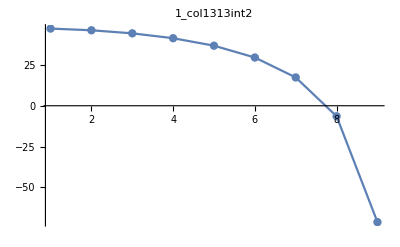
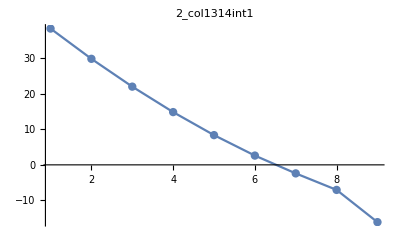
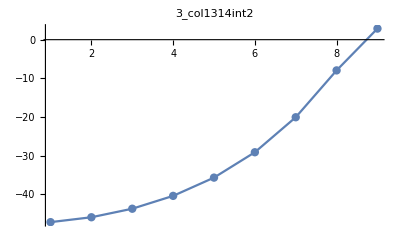
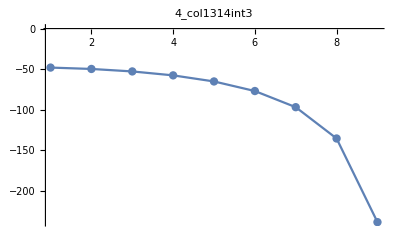
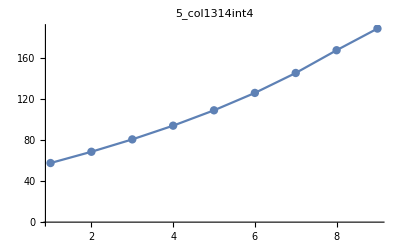
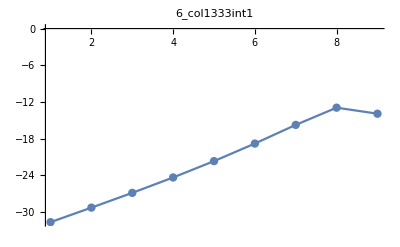
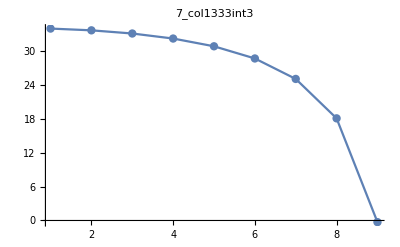
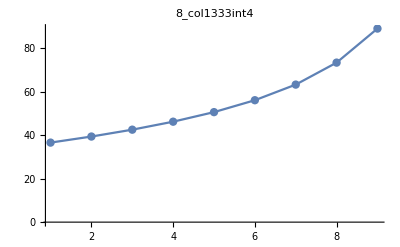

```mathematica
graphlist
```

```mathematica
mylist[[41]]
```

col14int4

## Gauge bubble (gg)

```mathematica
WriteTableBubble[fname_,entrylist_]:=Module[{entry,outfile,bubline},
entry=Sequence@@entrylist;
outfile=OpenWrite[fname];
Do[
bubline=resbubblegg[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta-> i*Delta+0.1,theta-> Pi/4}//N;
WriteString[outfile,i*Delta+0.1,"  ",Coefficient[bubline,ep,-2],"  ",Coefficient[bubline,ep,-1],"  ",Coefficient[bubline,ep,0]/.NNIntegrate-> NIntegrate,"\n"]
,{i,0,1/Delta-1}]
Close[fname];
]
```

```mathematica
WriteTableBubble["tablebub11gg.dat",{1,1}];
WriteTableBubble["tablebub12gg.dat",{1,2}];
WriteTableBubble["tablebub13gg.dat",{1,3}];
WriteTableBubble["tablebub22gg.dat",{2,2}];
WriteTableBubble["tablebub23gg.dat",{2,3}];
WriteTableBubble["tablebub33gg.dat",{3,3}];
```

## Quark bubble (gg)

```mathematica
WriteTableBubble[fname_,entrylist_]:=Module[{entry,outfile,bubline},
entry=Sequence@@entrylist;
outfile=OpenWrite[fname];
Do[
bubline=resquarkgg[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta-> i*Delta+0.1,theta-> Pi/4}//N;
WriteString[outfile,i*Delta+0.1,"  ",Coefficient[bubline,ep,-2],"  ",Coefficient[bubline,ep,-1],"  ",Coefficient[bubline,ep,0]/.NNIntegrate-> NIntegrate,"\n"]
,{i,0,1/Delta-1}]
Close[fname];
]
```

```mathematica
WriteTableBubble["tableqbub11gg.dat",{1,1}];
WriteTableBubble["tableqbub12gg.dat",{1,2}];
WriteTableBubble["tableqbub13gg.dat",{1,3}];
WriteTableBubble["tableqbub22gg.dat",{2,2}];
WriteTableBubble["tableqbub23gg.dat",{2,3}];
WriteTableBubble["tableqbub33gg.dat",{3,3}];
```

## Tadpole (gg)

```mathematica
WriteTableTadpole[fname_,entrylist_]:=Module[{entry,outfile,bubline},
entry=Sequence@@entrylist;
outfile=OpenWrite[fname];
Do[
tadline=restadpolegg[[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3}/.{beta-> i*Delta+0.1,theta-> Pi/4}//N;
Print[i*Delta+0.1,"  ",Coefficient[tadline,ep,-2],"  ",Coefficient[tadline,ep,-1],"  ",Coefficient[tadline,ep,0]/.NNIntegrate-> NIntegrate, "       ", tadline/.NNIntegrate-> NIntegrate//Expand]
WriteString[outfile,i*Delta+0.1,"  ",CForm[Coefficient[tadline,ep,-2]],"  ",Coefficient[tadline,ep,-1],"  ",Coefficient[tadline,ep,0]/.NNIntegrate-> NIntegrate,"\n"]
,{i,0,1/Delta-1}]
Close[fname];
]
```

```mathematica
WriteTableTadpole["tabletad11gg.dat",{1,1}];
WriteTableTadpole["tabletad12gg.dat",{1,2}];
WriteTableTadpole["tabletad13gg.dat",{1,3}];
WriteTableTadpole["tabletad22gg.dat",{2,2}];
WriteTableTadpole["tabletad23gg.dat",{2,3}];
WriteTableTadpole["tabletad33gg.dat",{3,3}];
```

0.1  -48.6426  -97.4485  -275.074       -275.074-48.6426/ep^2-97.4485/ep

0.3  -53.9802  -109.692  -309.948       -309.948-53.9802/ep^2-109.692/ep

0.5  -65.9167  -138.554  -392.723       -392.723-65.9167/ep^2-138.554/ep

0.7  -88.6133  -200.089  -572.863       -572.863-88.6133/ep^2-200.089/ep

0.9  -142.118  -391.935  -1182.55       -1182.55-142.118/ep^2-391.935/ep

0.1  5.09968  10.1994  28.7874       28.7874+5.09968/ep^2+10.1994/ep

0.3  15.509  31.018  87.5473       87.5473+15.509/ep^2+31.018/ep

0.5  26.6039  53.2079  150.177       150.177+26.6039/ep^2+53.2079/ep

0.7  39.0692  78.1384  220.543       220.543+39.0692/ep^2+78.1384/ep

0.9  54.1507  108.301  305.677       305.677+54.1507/ep^2+108.301/ep

0.1  0  0  0.       0.

0.3  0  0  0.       0.

0.5  0  0  0.       0.

0.7  0  0  0.       0.

0.9  0  0  0.       0.

0.1  2.90414  5.5461  15.6067       15.6067+2.90414/ep^2+5.5461/ep

0.3  2.07056  1.61134  4.05318       4.05318+2.07056/ep^2+1.61134/ep

0.5  -0.0422723  -8.31496  -25.409       -25.409-0.0422723/ep^2-8.31496/ep

0.7  -5.05396  -32.0317  -97.6259       -97.6259-5.05396/ep^2-32.0317/ep

0.9  -21.9391  -118.585  -383.332       -383.332-21.9391/ep^2-118.585/ep

0.1  2.12487  4.24973  11.9947       11.9947+2.12487/ep^2+4.24973/ep

0.3  6.46208  12.9242  36.478       36.478+6.46208/ep^2+12.9242/ep

0.5  11.085  22.1699  62.5739       62.5739+11.085/ep^2+22.1699/ep

0.7  16.2788  32.5577  91.893       91.893+16.2788/ep^2+32.5577/ep

0.9  22.5628  45.1256  127.366       127.366+22.5628/ep^2+45.1256/ep

0.1  1.61341  3.08117  8.67037       8.67037+1.61341/ep^2+3.08117/ep

0.3  1.15031  0.895188  2.25177       2.25177+1.15031/ep^2+0.895188/ep

0.5  -0.0234846  -4.61942  -14.1161       -14.1161-0.0234846/ep^2-4.61942/ep

0.7  -2.80775  -17.7954  -54.2366       -54.2366-2.80775/ep^2-17.7954/ep

0.9  -12.1884  -65.8805  -212.962       -212.962-12.1884/ep^2-65.8805/ep

## 2-cut (gg)

```mathematica
Repl2cutFinal=<<"final-2cut/replacements2cut.m";
Err2cutFinal=<<"final-2cut/errors2cut.m";
```

```mathematica
errform2c=(form2cgg/.Nc-> 3//Expand)/.num_/; NumberQ[num]-> Abs[num];
errNtoMseries=Expand[NtoMseries]/.Times[num_,arg2_]/; NumberQ[num]-> Times[Abs[num],arg2];
replfunc[beta_,theta_,repl_]:=Cases[repl,HoldPattern[col[arg1_][beta,theta][arg2_] -> rhs__],-1]/.{col[arg1_][__][arg2_]:>  ToExpression[ToString[arg1]<>"int"<>ToString[arg2]]}
res2cutfunc[be_,th_]:=form2cgg/.replfunc[be,th,Repl2cutFinal]
err2cutfunc[be_,th_]:=errform2c/.replfunc[be,th,Err2cutFinal]
```

```mathematica
WriteTable2Cut[fname_,entrylist_]:=Module[{entry,outfile,bubline},
entry=Sequence@@entrylist;
outfile=OpenWrite[fname];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
Print[0.1+Delta*i,"     ",
 CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,-1}]],"  "
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,0}]],  "  "
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,-1}]],"  "
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,0}]],   "  "
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,1}]],  "  "
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,1}]],  "  "
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-3}]],   "  "
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  "
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  "
];
WriteString[outfile,0.1+Delta*i,"     ",
  CForm[ SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,-1}]],"  ",
CForm[ SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,-1}]],"  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,0}]],  "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,0}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,-1}]],"  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,-1}]],"  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,0}]],   "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-2},{ep,0,1}]],  "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,-2},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,-1},{ep,0,1}]],  "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,-1},{ep,0,1}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-3}]],   "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-3}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],  "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  "
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   " ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"
]
,{i,0,1/Delta-1}]
Close[fname];
]
```

```mathematica
WriteTable2Cut["table2cut11gg.dat",{1,1}];
WriteTable2Cut["table2cut12gg.dat",{1,2}];
WriteTable2Cut["table2cut13gg.dat",{1,3}];
WriteTable2Cut["table2cut22gg.dat",{2,2}];
WriteTable2Cut["table2cut23gg.dat",{2,3}];
WriteTable2Cut["table2cut33gg.dat",{3,3}];
```

0.1     0.0004304314458347603   0.00021237375807799263   0.00012057805613118258   0.018887614903889887   -0.00007254953147588498   -0.030427528073725774   -0.641656318200812   49.73156603316372   97.75819338455973

0.3     0.0004304314458347603   0.00021237375807799263   0.0038942611796985147   -0.001561999803224542   -0.00007254953147588498   -0.013178019102665061   -5.976865791000809   64.26286078023311   112.27854874605009

0.5     0.0004304314458347603   0.00021237375807799263   0.004342029938036161   -0.022015253561805077   -0.00007254953147588498   0.0027387086582544196   -17.91729165855081   98.45014261615444   145.90676965057966

0.7     0.0004304314458347603   0.00021237375807799263   0.005791208681301858   -0.03769791201627354   -0.00007254953147588498   0.014109257614026087   -40.619189527327514   168.8443266434259   214.01774830362334

0.9     0.0004304314458347603   0.00021237375807799263   0.010508540364770277   0.11641915850671271   -0.00007254953147588498   -0.21549902782132818   -94.1203948077008   350.7025018317751   417.51056195804233

0.1     0   0   -0.000495649150884545   0.01302249897491819   0   -0.018253534280572747   5.099473335793697   5.018367050492435   -16.7648699992503

0.3     0   0   -0.0014666585997940244   -0.001076252051076055   0   0.0023035759788443966   15.509240953878281   13.25194101289389   -50.6590227519629

0.5     0   0   -0.0029709572386886446   0.005204727738465945   0   -0.005492032792529165   26.602163163453973   14.772856688697502   -85.947303608672

0.7     0   0   -0.0026371683966872504   0.01886879771590548   0   -0.028200478717468853   39.06683657152634   -1.98196810175724   -125.44194894487904

0.9     0   0   -0.005303021268540323   0.07801368032107366   0   -0.10803680654991485   54.14754795393805   -90.26520016192568   -197.1544797241484

0.1     0.00017934643576448346   0.00008848906586583026   0.00005024085672132605   0.007869839543287451   -0.000030228971448285403   -0.012678136697385737   0.003629462749664779   0.40418074597776715   -0.004622043041053334

0.3     0.00017934643576448346   0.00008848906586583026   0.001622608824874381   -0.0006508332513435592   -0.000030228971448285403   -0.005490841292777109   0.003739278249665444   3.7131349056193472   -0.0022961956447770833

0.5     0.00017934643576448346   0.00008848906586583026   0.0018091791408484004   -0.009173022317418783   -0.000030228971448285403   0.0011411286076060084   0.0027331919371639994   10.923908751776166   0.0027796278743324153

0.7     0.00017934643576448346   0.00008848906586583026   0.0024130036172091075   -0.015707463340113973   -0.000030228971448285403   0.0058788573391775345   0.001560455946865575   23.558170832066608   0.008361011889734853

0.9     0.00017934643576448346   0.00008848906586583026   0.004378558485320948   0.0485079827111303   -0.000030228971448285403   -0.08979126159222008   0.00166045912466337   45.253320610662634   -0.007509598551213657

0.1     0.0005918432380227954   0.00029201391735723985   -0.0032736113234003955   0.016395339414336553   -0.00009975560577934185   -0.013208411068960832   26.905761903103997   68.96205678689887   -67.59442002123858

0.3     0.0005918432380227954   0.00029201391735723985   -0.0015301279631423476   -0.00017086696176617103   -0.00009975560577934185   0.004647526042530981   26.07400835284238   73.37179940024248   -64.86160272016741

0.5     0.0005918432380227954   0.00029201391735723985   -0.002357630021759217   0.010809806537071606   -0.00009975560577934185   -0.01622254441465934   23.962609876838684   82.49812149164686   -58.08588987218908

0.7     0.0005918432380227954   0.00029201391735723985   -0.0023854224606335   0.045105119770357076   -0.00009975560577934185   -0.06906914964261557   18.950040324741916   96.36210695038473   -42.68495614412701

0.9     0.0005918432380227954   0.00029201391735723985   -0.004132828160280875   0.11315681223467808   -0.00009975560577934185   -0.15599340169082526   2.065165510912504   108.14410848656456   7.9605402318324

0.1     0   0   -0.000039270710033168974   0.010815615298719366   0   -0.015611729281197133   2.124678315174457   4.233745612098474   -6.996217987795546

0.3     0   0   -0.00020372985788662224   -0.0006558788455843531   0   -0.0006651329801109683   6.461761879126368   12.477646265840573   -21.309067093653823

0.5     0   0   -0.001479896265329775   0.004429459734357002   0   -0.005406264469103216   11.083676682095406   19.67118929806637   -36.81352625677761

0.7     0   0   -0.002609685219281522   0.015317288080127476   0   -0.018909909269334724   16.27755010433595   22.844273863998854   -55.42961055565749

0.9     0   0   -0.006387375738303695   0.051583447621367184   0   -0.06059387878548479   22.561520996734604   3.4444735940794318   -90.8513554867885

0.1     0.00020923750839189735   0.00010323724351013529   -0.0018521668619255487   0.003861962201328669   -0.000035267133356332975   0.0011140849821678128   14.945225859891337   38.04279993984751   -37.54937420532737

0.3     0.00020923750839189735   0.00010323724351013529   -0.001931810307217559   0.0003389627443589416   -0.000035267133356332975   0.006242519774368623   14.483067343857101   38.28668750749961   -36.032692936329816

0.5     0.00020923750839189735   0.00010323724351013529   -0.0025159138837651663   0.012120796287763412   -0.000035267133356332975   -0.009773277079881409   13.310738914730052   38.549683883064155   -32.271791903132396

0.7     0.00020923750839189735   0.00010323724351013529   -0.0029339037784913476   0.03553004209916324   -0.000035267133356332975   -0.042290988027571454   10.526759876447601   37.8290566399471   -23.71943853244151

0.9     0.00020923750839189735   0.00010323724351013529   -0.005215054634814453   0.030526240545178728   -0.000035267133356332975   -0.026802159877867313   1.1462071999793928   29.911179863205238   4.4275287500521845

## Alternative derivation: maximal use of RGE (gg)

```mathematica
Delta=1/10;
```

```mathematica
Replf=Table[f[i,j]-> Coefficient[Coefficient[NtoMseries/.{ap-> 0,mu-> 1},ep,i],Lp,j],{i,-1,1},{j,-1,2}]//Flatten
```

{f[-1,-1]→0,f[-1,0]→-1.,f[-1,1]→0,f[-1,2]→0,f[0,-1]→0,f[0,0]→1.38629,f[0,1]→0,f[0,2]→0,f[1,-1]→0,f[1,0]→0.684028,f[1,1]→0,f[1,2]→0}

```mathematica
ReplParameters={ap->0 ,mu-> 1,Lp-> 0,Nc-> 3};
```

```mathematica
singlecutmatrix=Read["matrix1c-gg.dat"];Close["matrix1c-gg.dat"];
```

### ep1

```mathematica
Do[
tmpbeta=i*Delta+0.1;
ReplValues={beta-> tmpbeta,theta-> Pi/4};
s[-1][tmpbeta]=-resReep2outgg/f[-1,0]/.Replf/.ReplParameters/.ReplValues//N;
sbub[0][tmpbeta]=(Coefficient[resbubblegg/NtoMseries/.ReplParameters,ep,0])/.ReplValues//N;
stad[0][tmpbeta]=Coefficient[restadpolegg/NtoMseries/.ReplParameters,ep,0]/.ReplValues//N;
s2cut[0][tmpbeta]=Coefficient[Coefficient[res2cutfunc[tmpbeta,0.785398],ap,0],ep,0]/.ReplParameters;
s1cut[0][tmpbeta]=Coefficient[Coefficient[singlecutmatrix[[i+1]]/NtoMseries,ap,0],ep,0];
s[0][tmpbeta]=sbub[0][tmpbeta]+stad[0][tmpbeta]+s1cut[0][tmpbeta]+s2cut[0][tmpbeta];
(*resep1alt[tmpbeta]=(f[-1,0]s[-1][tmpbeta])/.Replf;*)
resep1alt1[tmpbeta]=(f[-1,0]s[0][tmpbeta]+f[0,0]s[-1][tmpbeta])/.Replf;
,{i,0,1/Delta-2}];
```

### ep0

```mathematica
Do[
tmpbeta=i*Delta+0.1;
ReplValues={beta-> tmpbeta,theta-> Pi/4};
s[0][tmpbeta]=(-resReep1outgg-f[0,0]s[-1][tmpbeta])/f[-1,0]/.ReplParameters/.ReplValues;
sbub[1][tmpbeta]=SeriesCoefficient[resbubblegg/NtoMseries/.ReplParameters,{ap,0,0},{ep,0,1}]/.ReplValues/.NNIntegrate-> NIntegrate//N;
stad[1][tmpbeta]=SeriesCoefficient[restadpolegg/NtoMseries/.ReplParameters,{ap,0,0},{ep,0,1}]/.ReplValues/.NNIntegrate-> NIntegrate//N;
s2cut[1][tmpbeta]=Coefficient[Coefficient[res2cutfunc[tmpbeta,0.785398],ap,0],ep,1]/.ReplParameters;
s1cut[1][tmpbeta]=SeriesCoefficient[singlecutmatrix[[i+1]]/NtoMseries,{ap,0,0},{ep,0,1}];
s[1][tmpbeta]=sbub[1][tmpbeta]+stad[1][tmpbeta]+s1cut[1][tmpbeta]+s2cut[1][tmpbeta];
resep1alt0[tmpbeta]=(f[-1,0]s[1][tmpbeta]+f[0,0]s[0][tmpbeta]+f[1,0]s[-1][tmpbeta])/.Replf;
line2cuterr2[tmpbeta]=errNtoMseries err2cutfunc[tmpbeta,0.785398]/.{mu-> 1,Lp-> 0,Nc-> 3};
,{i,0,1/Delta-2}];
```

```mathematica
outfile=OpenWrite["tablealtgg.dat"];
Do[
tmpbeta=i*Delta+0.1;
WriteString[outfile,tmpbeta,"     ",
CForm[ resep1alt0[tmpbeta][[1,1]]],"  ",
CForm[SeriesCoefficient[line2cuterr2[tmpbeta][[1,1]],{ap,0,0},{ep,0,0}]], "  ",
CForm[ resep1alt0[tmpbeta][[1,2]]],"  ",
CForm[SeriesCoefficient[line2cuterr2[tmpbeta][[1,2]],{ap,0,0},{ep,0,0}]], "  ",
CForm[ resep1alt0[tmpbeta][[1,3]]],"  ",
CForm[SeriesCoefficient[line2cuterr2[tmpbeta][[1,3]],{ap,0,0},{ep,0,0}]], "  ",
CForm[ resep1alt0[tmpbeta][[2,2]]],"  ",
CForm[SeriesCoefficient[line2cuterr2[tmpbeta][[2,2]],{ap,0,0},{ep,0,0}]], "  ",
CForm[ resep1alt0[tmpbeta][[2,3]]],"  ",
CForm[SeriesCoefficient[line2cuterr2[tmpbeta][[2,3]],{ap,0,0},{ep,0,0}]], "  ",
CForm[ resep1alt0[tmpbeta][[3,3]]],"  ",
CForm[SeriesCoefficient[line2cuterr2[tmpbeta][[3,3]],{ap,0,0},{ep,0,0}]], "  ",
 "\n"

]
,{i,0,1/Delta-2}]
Close["tablealtgg.dat"];
```

```mathematica
SeriesCoefficient[line2cuterr2[tmpbeta],{ap,0,0},{ep,0,0}]
```

{{8.38192,4.23007,0.681666},{4.23007,5.03032,1.86083},{0.681666,1.86083,2.56965}}

# Validation with tadpole and bubble

## Tadpole (qq)

```mathematica
ReplTad=<<"runs-sfcalc/final-tadpole/replacementstad.m";
ReplTadErr=<<"runs-sfcalc/final-tadpole/errorstad.m";
```

```mathematica
ReplNamesInMaster=Flatten[Table[Thread["gtad"<>ToString[i]<>ToString[j]->ToExpression[ "colgtad"<>ToString[i]<>ToString[j]<>"int1"]],{i,1,4},{j,1,4}]];
```

```mathematica
names={{colgtad13,colgtad14},{colgtad23,colgtad24}};
ReplNegativeBeta=Table[col[names[[i]][[1]]][arg1_,arg2_][arg3_]/;arg1<0-> col[names[[i]][[2]]][-arg1,arg2][arg3],{i,1,Length[names]}];
```

```mathematica
errformtad=(tadpolemaster/.Nc-> 3//Expand) /.num_/; NumberQ[num]-> Abs[num];
errNtoMseries=Expand[NtoMseries]/.Times[num_,arg2_]/; NumberQ[num]-> Times[Abs[num],arg2];
replfunc[beta_,theta_,repl_]:=Cases[repl,HoldPattern[col[arg1_][beta,theta][arg2_] -> rhs__],-1]/.{col[arg1_][__][arg2_]:>  ToExpression[ToString[arg1]<>"int"<>ToString[arg2]]};
res2cutfunc[be_,th_]:=tadpolemaster/.ReplNamesInMaster/.replfunc[be,th,ReplTad/.ReplNegativeBeta]
err2cutfunc[be_,th_]:=errformtad/."gtad13"-> 0/.ReplNamesInMaster/.replfunc[be,th,ReplTadErr/.ReplNegativeBeta]
```

```mathematica
Delta  = 1/5;
```

```mathematica
entry=Sequence[1,1];
outfile=OpenWrite["tabletad11valid.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "  "];
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close["tabletad11valid.dat"];
```

0.1     -48.64117896  -97.44752060952854  -275.0725269671979  0.00024939065412  0.005451161389522558  0.027845937830275225

0.3     -53.978627508  -109.69102550466857  -309.94497162102675  0.00027714902820000003  0.0060129819521835175  0.0307396748564886

0.5     -65.9147712  -138.55127233093222  -392.71801437671866  0.0003571679262000001  0.007291791095263946  0.03724489796351433

0.7     -88.610696652  -200.0849024164272  -572.8537758411646  0.0005987261772000001  0.009910188802507228  0.050223129274054555

0.9     -142.11396312  -391.92436741034385  -1182.5380247609316  0.0016618612224  0.01826942040957693  0.09409875656772973

```mathematica
entry=Sequence[1,2];
outfile=OpenWrite["tabletad12valid.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close["tabletad12valid.dat"];
```

0.1     2.2665141339999995  4.532335296637266  12.794569210020509

0.3     6.892742522  13.784233309100104  38.91572868506829

0.5     11.823963202  23.648208726978307  66.73770558655654

0.7     17.364662906  34.730578266664466  98.04387247935233

0.9     24.068159846  48.14052100895802  135.90745149192242

```mathematica
entry=Sequence[2,2];
outfile=OpenWrite["tabletad22valid.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close["tabletad22valid.dat"];
```

0.1     2.2325338676666657  4.336484741577854  12.182983750561018

0.3     3.7898894530000002  6.44301766870502  17.931029459561934

0.5     4.905591223333333  6.140155585800436  16.52061392557771

0.7     4.986469571666666  0.2153556889025845  -2.6258682546012935

0.9     0.2742534510000003  -32.6710346479723  -113.83447812761818

## Gauge bubble (qq)

```mathematica
ReplBub=<<"runs-sfcalc/final-bubble/replacementsbubble.m";
ReplBubErr=<<"runs-sfcalc/final-bubble/errorsbubble.m";
```

```mathematica
ReplNamesInMaster=Flatten[Table[Thread["ggau"<>ToString[i]<>ToString[j]->ToExpression[ "colggau"<>ToString[i]<>ToString[j]<>"int1"]],{i,1,4},{j,1,4}]];
```

```mathematica
names={{colgbub13,colgbub14},{colgbub23,colgbub24}};
ReplNegativeBeta=Table[col[names[[i]][[1]]][arg1_,arg2_][arg3_]/;arg1<0-> col[names[[i]][[2]]][-arg1,arg2][arg3],{i,1,Length[names]}];
```

```mathematica
ReplSetToZero=Table[Flatten[names][[i]][_]-> 0,{i,1,4}];
```

```mathematica
names2={gbub13,gbub14, gbub23,gbub24,gbub34};
ReplModMaster=Table[ToString[names2[[i]]]-> Sum[ToExpression["col"<>ToString[names2[[i]]]<>"["<>ToString[j]<>"]"],{j,1,15}],{i,1,Length[names2]}];
```

```mathematica
errformbub=(gaugemaster/.Nc-> 3//Expand)/.num_/; NumberQ[num]-> Abs[num];
errNtoMseries=Expand[NtoMseries]/.Times[num_,arg2_]/; NumberQ[num]-> Times[Abs[num],arg2];
replfunc[beta_,theta_,repl_]:=Cases[repl,HoldPattern[col[arg1_][beta,theta][arg2_] -> rhs__],-1]/.{col[arg1_][__][arg2_]:>  ToExpression[ToString[arg1]<>"["<>ToString[arg2]<>"]"]};
res2cutfunc[be_,th_]:=gaugemaster/.ReplModMaster/.replfunc[be,th,ReplBub/.ReplNegativeBeta]/.ReplSetToZero
err2cutfunc[be_,th_]:=errformbub/.ReplModMaster/.replfunc[be,th,ReplBubErr/.ReplNegativeBeta]/.ReplSetToZero
```

```mathematica
Delta  = 1/5;
```

```mathematica
entry=Sequence[1,1];
outfile=OpenWrite["tablebub11valid.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close["tablebub11valid.dat"];
```

0.1     -0.5344636308000048  -0.8377925063983395  -2.288019384609835

0.3     -4.9824602171999945  -7.877687413191447  -21.479662278584225

0.5     -14.929269853199997  -24.1186481660717  -65.22826567601244

0.7     -33.84258345479999  -57.60280835568154  -153.23345467992846

0.9     -78.42951656519998  -160.50284278270414  -418.06396220220194

```mathematica
entry=Sequence[1,2];
outfile=OpenWrite["tablebub12valid.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close["tablebub12valid.dat"];
```

0.1     1.8887565448000032  3.9026290188154555  10.997267216135455

0.3     5.743911231199999  11.869299355814222  33.45037993002049

0.5     9.853284847999998  20.363488550709548  57.361872069354966

0.7     14.470574970160001  29.906595305944553  84.27489413469159

0.9     20.056812218399998  41.454197239591565  116.82426730373533

```mathematica
entry=Sequence[2,2];
outfile=OpenWrite["tablebub22valid.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close["tablebub22valid.dat"];
```

0.1     10.749115197333333  22.196214760508667  62.49937885474847

0.3     12.046886503133333  24.80678014812161  69.85190761084769

0.5     12.976570565000001  26.499202794132806  74.77832255684932

0.7     13.043943533880004  25.80080992032921  73.22887449131075

0.9     9.116842130466669  11.45365438171381  35.421477253510005

## Quark bubble (qq)

```mathematica
ReplBub=<<"runs-sfcalc/final-qbub/replacementsqbub.m";
ReplBubErr=<<"runs-sfcalc/final-qbub/errorsqbub.m";
```

```mathematica
ReplNamesInMaster=Flatten[Table[Thread["gquark"<>ToString[i]<>ToString[j]->ToExpression[ "colqbub"<>ToString[i]<>ToString[j]<>"int1"]],{i,1,4},{j,1,4}]];
```

```mathematica
names={{colqbub13,colqbub14},{colqbub23,colqbub24}};
ReplNegativeBeta=Table[col[names[[i]][[1]]][arg1_,arg2_][arg3_]/;arg1<0-> col[names[[i]][[2]]][-arg1,arg2][arg3],{i,1,Length[names]}];
```

```mathematica
ReplSetToZero=Table[Flatten[names][[i]][_]-> 0,{i,1,4}];
```

```mathematica
names2={qbub13,qbub14, qbub23,qbub24,qbub34};
ReplModMaster=Table[ToString[names2[[i]]]-> Sum[ToExpression["col"<>ToString[names2[[i]]]<>"["<>ToString[j]<>"]"],{j,1,15}],{i,1,Length[names2]}];
```

```mathematica
errformbub=(quarkmaster/.Nc-> 3//Expand)/.num_/; NumberQ[num]-> Abs[num];
errNtoMseries=Expand[NtoMseries]/.Times[num_,arg2_]/; NumberQ[num]-> Times[Abs[num],arg2];
replfunc[beta_,theta_,repl_]:=Cases[repl,HoldPattern[col[arg1_][beta,theta][arg2_] -> rhs__],-1]/.{col[arg1_][__][arg2_]:>  ToExpression[ToString[arg1]<>"["<>ToString[arg2]<>"]"]};
res2cutfunc[be_,th_]:=1/2 quarkmaster/.ReplModMaster/.replfunc[be,th,ReplBub/.ReplNegativeBeta]/.ReplSetToZero
err2cutfunc[be_,th_]:=1/2 errformbub/.ReplModMaster/.replfunc[be,th,ReplBubErr/.ReplNegativeBeta]/.ReplSetToZero
```

```mathematica
Delta  = 1/5;
```

```mathematica
entry=Sequence[1,1];
outfile=OpenWrite["tableqbub11valid.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3,nf-> 1,TF-> 1};
line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3,nf-> 1,TF-> 1};
Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close["tableqbub11valid.dat"];
```

0.1     0.07136034080000098  0.08292711594137556  0.24666156814264034

0.3     0.6644641764000019  0.7842486170905179  2.2826127619296788

0.5     1.9906879780000013  2.419133307749428  6.9317523094536995

0.7     4.512464050000001  5.874743976328758  16.27418962314267

0.9     10.457341276400001  17.2172378090204  44.674267015314236

```mathematica
entry=Sequence[1,2];
outfile=OpenWrite["tableqbub12valid.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3,nf-> 1,TF-> 1};
line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3,nf-> 1,TF-> 1};
Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close["tableqbub12valid.dat"];
```

0.1     -0.2518339518666668  -0.41957822592203414  -1.186718918445224

0.3     -0.765851091466667  -1.2761397231089133  -3.643198919817846

0.5     -1.3137708200666665  -2.1895077535377254  -6.24992410015261

0.7     -1.9294145055799998  -3.215669368584857  -9.165220704865032

0.9     -2.6742440982666666  -4.457487590314772  -12.724446824547718

```mathematica
entry=Sequence[2,2];
outfile=OpenWrite["tableqbub22valid.dat"];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3,nf-> 1,TF-> 1};
line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3,nf-> 1,TF-> 1};
Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close["tableqbub22valid.dat"];
```

0.1     -1.4331467650666672  -2.3858925065975343  -6.810042129804438

0.3     -1.606174092377778  -2.6647407724264984  -7.603000367407573

0.5     -1.7301455052888894  -2.840723045745533  -8.128481170556524

0.7     -1.7391312953844444  -2.7440378617391956  -7.97293020061271

0.9     -1.2154985570000003  -1.0405031897482016  -3.818805885826634

## Gauge bubble (gg)

```mathematica
ReplBub=<<"runs-sfcalc/final-bubble/replacementsbubble.m";
ReplBubErr=<<"runs-sfcalc/final-bubble/errorsbubble.m";
```

```mathematica
ReplNamesInMaster=Flatten[Table[Thread["ggau"<>ToString[i]<>ToString[j]->ToExpression[ "colggau"<>ToString[i]<>ToString[j]<>"int1"]],{i,1,4},{j,1,4}]];
```

```mathematica
names={{colgbub13,colgbub14},{colgbub23,colgbub24}};
ReplNegativeBeta=Table[col[names[[i]][[1]]][arg1_,arg2_][arg3_]/;arg1<0-> col[names[[i]][[2]]][-arg1,arg2][arg3],{i,1,Length[names]}];
```

```mathematica
ReplSetToZero=Table[Flatten[names][[i]][_]-> 0,{i,1,4}];
```

```mathematica
names2={gbub13,gbub14, gbub23,gbub24,gbub34};
ReplModMaster=Table[ToString[names2[[i]]]-> Sum[ToExpression["col"<>ToString[names2[[i]]]<>"["<>ToString[j]<>"]"],{j,1,15}],{i,1,Length[names2]}];
```

```mathematica
errformbub=(gaugemasterGG/.Nc-> 3//Expand)/.num_/; NumberQ[num]-> Abs[num];
errNtoMseries=Expand[NtoMseries]/.Times[num_,arg2_]/; NumberQ[num]-> Times[Abs[num],arg2];
replfunc[beta_,theta_,repl_]:=Cases[repl,HoldPattern[col[arg1_][beta,theta][arg2_] -> rhs__],-1]/.{col[arg1_][__][arg2_]:>  ToExpression[ToString[arg1]<>"["<>ToString[arg2]<>"]"]};
res2cutfunc[be_,th_]:=gaugemasterGG/.ReplModMaster/.replfunc[be,th,ReplBub/.ReplNegativeBeta]/.ReplSetToZero
err2cutfunc[be_,th_]:=errformbub/.ReplModMaster/.replfunc[be,th,ReplBubErr/.ReplNegativeBeta]/.ReplSetToZero
```

```mathematica
Delta  = 1/5;
```

```mathematica
WriteTable[fname_,entrylist_]:=Module[{entry,line2cut,line2cuterr},
entry=Sequence@@entrylist;
outfile=OpenWrite[fname];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3};
(*Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];*)
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close[fname];
]
```

```mathematica
WriteTable["tablebub11validgg.dat",{1,1}];
WriteTable["tablebub13validgg.dat",{1,2}];
WriteTable["tablebub13validgg.dat",{1,3}];
WriteTable["tablebub22validgg.dat",{2,2}];
WriteTable["tablebub23validgg.dat",{2,3}];
WriteTable["tablebub33validgg.dat",{3,3}];
```

## Quark bubble (gg)

```mathematica
ReplBub=<<"runs-sfcalc/final-qbub/replacementsqbub.m";
ReplBubErr=<<"runs-sfcalc/final-qbub/errorsqbub.m";
```

```mathematica
ReplNamesInMaster=Flatten[Table[Thread["gquark"<>ToString[i]<>ToString[j]->ToExpression[ "colqbub"<>ToString[i]<>ToString[j]<>"int1"]],{i,1,4},{j,1,4}]];
```

```mathematica
names={{colqbub13,colqbub14},{colqbub23,colqbub24}};
ReplNegativeBeta=Table[col[names[[i]][[1]]][arg1_,arg2_][arg3_]/;arg1<0-> col[names[[i]][[2]]][-arg1,arg2][arg3],{i,1,Length[names]}];
```

```mathematica
ReplSetToZero=Table[Flatten[names][[i]][_]-> 0,{i,1,4}];
```

```mathematica
names2={qbub13,qbub14, qbub23,qbub24,qbub34};
ReplModMaster=Table[ToString[names2[[i]]]-> Sum[ToExpression["col"<>ToString[names2[[i]]]<>"["<>ToString[j]<>"]"],{j,1,15}],{i,1,Length[names2]}];
```

```mathematica
errformbub=(quarkmasterGG/.Nc-> 3//Expand)/.num_/; NumberQ[num]-> Abs[num];
errNtoMseries=Expand[NtoMseries]/.Times[num_,arg2_]/; NumberQ[num]-> Times[Abs[num],arg2];
replfunc[beta_,theta_,repl_]:=Cases[repl,HoldPattern[col[arg1_][beta,theta][arg2_] -> rhs__],-1]/.{col[arg1_][__][arg2_]:>  ToExpression[ToString[arg1]<>"["<>ToString[arg2]<>"]"]};
res2cutfunc[be_,th_]:=quarkmasterGG/.ReplModMaster/.replfunc[be,th,ReplBub/.ReplNegativeBeta]/.ReplSetToZero
err2cutfunc[be_,th_]:=errformbub/.ReplModMaster/.replfunc[be,th,ReplBubErr/.ReplNegativeBeta]/.ReplSetToZero
```

```mathematica
Delta  = 1/5;
```

```mathematica
WriteTable[fname_,entrylist_]:=Module[{entry,line2cut,line2cuterr},
entry=Sequence@@entrylist;
outfile=OpenWrite[fname];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3,TF-> 1/2,nf-> 1};line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3,TF-> 1/2,nf-> 1};
(*Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];*)
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close[fname];
]
```

```mathematica
WriteTable["tableqbub11validgg.dat",{1,1}];
WriteTable["tableqbub12validgg.dat",{1,2}];
WriteTable["tableqbub13validgg.dat",{1,3}];
WriteTable["tableqbub22validgg.dat",{2,2}];
WriteTable["tableqbub23validgg.dat",{2,3}];
WriteTable["tableqbub33validgg.dat",{3,3}];
```

## Tadpole (gg)

```mathematica
ReplTad=<<"runs-sfcalc/final-tadpole/replacementstad.m";
ReplTadErr=<<"runs-sfcalc/final-tadpole/errorstad.m";
```

```mathematica
ReplNamesInMaster=Flatten[Table[Thread["gtad"<>ToString[i]<>ToString[j]->ToExpression[ "colgtad"<>ToString[i]<>ToString[j]<>"int1"]],{i,1,4},{j,1,4}]];
```

```mathematica
names={{colgtad13,colgtad14},{colgtad23,colgtad24}};
ReplNegativeBeta=Table[col[names[[i]][[1]]][arg1_,arg2_][arg3_]/;arg1<0-> col[names[[i]][[2]]][-arg1,arg2][arg3],{i,1,Length[names]}];
```

```mathematica
errformtad=(tadpolemasterGG/.Nc-> 3//Expand) /.num_/; NumberQ[num]-> Abs[num];
errNtoMseries=Expand[NtoMseries]/.Times[num_,arg2_]/; NumberQ[num]-> Times[Abs[num],arg2];
replfunc[beta_,theta_,repl_]:=Cases[repl,HoldPattern[col[arg1_][beta,theta][arg2_] -> rhs__],-1]/.{col[arg1_][__][arg2_]:>  ToExpression[ToString[arg1]<>"int"<>ToString[arg2]]};
res2cutfunc[be_,th_]:=tadpolemasterGG/.ReplNamesInMaster/.replfunc[be,th,ReplTad/.ReplNegativeBeta]
err2cutfunc[be_,th_]:=errformtad/."gtad13"-> 0/.ReplNamesInMaster/.replfunc[be,th,ReplTadErr/.ReplNegativeBeta]
```

```mathematica
Delta  = 1/5;
```

```mathematica
WriteTable[fname_,entrylist_]:=Module[{entry,line2cut,line2cuterr},
entry=Sequence@@entrylist;
outfile=OpenWrite[fname];
Do[
line2cut=NtoMseries res2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3,TF-> 1/2,nf-> 1};line2cuterr=errNtoMseries err2cutfunc[0.1+Delta*i,0.785398][[entry]]/.{mu-> 1,Lp-> 0,Nc-> 3,TF-> 1/2,nf-> 1};
(*Print[0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  "];*)
WriteString[outfile,0.1+Delta*i,"     ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cut,{ap,0,0},{ep,0,0}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-2}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,-1}]],   "  ",
CForm[SeriesCoefficient[line2cuterr,{ap,0,0},{ep,0,0}]],   "\n"];
,{i,0,1/Delta-1}]
Close[fname];
]
```

```mathematica
WriteTable["tabletad11validgg.dat",{1,1}];
WriteTable["tabletad12validgg.dat",{1,2}];WriteTable["tabletad13validgg.dat",{1,3}];WriteTable["tabletad22validgg.dat",{2,2}];WriteTable["tabletad23validgg.dat",{2,3}];WriteTable["tabletad33validgg.dat",{3,3}];
```

# Combination boundary

```mathematica
posbub=Limit[resbubble,beta-> 0]/.{theta-> 0,mu-> 1};
posbubep2=Coefficient[posbub,ep,-2]
posbubep1=Coefficient[posbub,ep,-1]/.Lp-> 0
posbubLp1=Collect[Coefficient[posbub,Lp,1],ep]
posbubLp2=Collect[Coefficient[posbub,Lp,2],ep]
```

{{0,0},{0,-5/12 Nc (1-Nc^2)}}

{{1/3 Nc (-1+Nc^2),0},{0,((24-248 Nc^2) (1-Nc^2))/(288 Nc)}}

{{2/3 Nc (-1+Nc^2),0},{0,-(5 Nc (1-Nc^2))/(6 ep)+((48-496 Nc^2) (1-Nc^2))/(288 Nc)}}

{{0,0},{0,-5/6 Nc (1-Nc^2)}}

```mathematica
postad=Limit[restadpole,beta-> 0]/.{theta-> 0,mu-> 1,Lp-> 0};
postadep2=Coefficient[postad,ep,-2]
postadep1=Coefficient[postad,ep,-1]
```

{{-2 Nc (-1+Nc^2),0},{0,(-1+Nc^2)/(2 Nc)}}

{{-4 Nc (-1+Nc^2),0},{0,(-1+Nc^2)/Nc}}

```mathematica
(*ReplExtra={col33int1-> 0};*)
(*ReplRemoveTadpole={col13int17-> 0,col13int18-> 0,col14int17-> 0,col14int18-> 0,col34int13-> 0};*)
res2cut=form2c/.ReplRemoveTadpole/.Repl2cutBoundaryAbelian/.Repl2cutBoundaryNonAbelian(*/.ReplExtra*)//Simplify;
Collect[res2cut,{ap,ep}]/.Nc-> 3//MatrixForm
```

(-0.00738693+(-0.00202511-0.00621908/ep)/ap^2+(-0.00275641+0.0111958/ep^2+0.00137366/ep)/ap+0.000094008/ep^2-0.102195/ep | 0.0012655+(-0.00236262-0.00725559/ep)/ap^2+(-0.00291949+0.0130618/ep^2+0.00057236/ep)/ap+0.00564512/ep
0.0012655+(-0.00236262-0.00725559/ep)/ap^2+(-0.00291949+0.0130618/ep^2+0.00057236/ep)/ap+0.00564512/ep | 242.803+(-0.00320642-0.00984688/ep)/ap^2+(0.00508808+0.0177321/ep^2+0.00402147/ep)/ap-48.0009/ep^2-121.383/ep)

```mathematica
pos2cut=prefacFT res2cut/.{Lp-> 0,mu-> 1}//Simplify;
pos2cutep3 =MyCoefficient[pos2cut,0,-3]//Simplify;
pos2cutep2 =MyCoefficient[pos2cut,0,-2]//Simplify;
pos2cutep1 =MyCoefficient[pos2cut,0,-1]//Simplify;
pos2cutep3//MatrixForm
pos2cutep2//MatrixForm
pos2cutep1//MatrixForm
```

(-0.000125232/Nc+0.000126211 Nc-9.7925×10^-7 Nc^3 | -0.00017175+0.000125232/Nc^2+0.0000465183 Nc^2
-0.00017175+0.000125232/Nc^2+0.0000465183 Nc^2 | -0.0000939238/Nc^3+0.000155408/Nc-0.500108 Nc+0.500047 Nc^3)

(0.000509194/Nc-0.0015691 Nc+0.0010599 Nc^3 | 0.000998419-0.000549849/Nc^2-0.000448571 Nc^2
0.000998419-0.000549849/Nc^2-0.000448571 Nc^2 | 0.00042255/Nc^3-0.000701759/Nc-1.32202 Nc+1.3223 Nc^3)

(0.00552747/Nc-0.00583587 Nc+0.000308399 Nc^3 | 0.0078571-0.00544303/Nc^2-0.00241407 Nc^2
0.0078571-0.00544303/Nc^2-0.00241407 Nc^2 | 0.00406116/Nc^3-0.00756944/Nc+1.15018 Nc-1.14667 Nc^3)

```mathematica
pos1cutep3=singlecutep3
pos1cutep2=singlecutep2
pos1cutep1=singlecutep1
```

{{0.,0.},{0.,0.5 Nc-0.5 Nc^3}}

{{0.,0.},{0.,0.322467 Nc-0.322467 Nc^3}}

{{0.,1.77636×10^-15-1.77636×10^-15 Nc^2},{1.77636×10^-15-1.77636×10^-15 Nc^2,-(1.77636×10^-15)/Nc-1.42348 Nc+1.42348 Nc^3}}

### ep3

```mathematica
pos1cutep3+pos2cutep3//MatrixForm
```

(0.-0.000125232/Nc+0.000126211 Nc-9.7925×10^-7 Nc^3 | -0.00017175+0.000125232/Nc^2+0.0000465183 Nc^2
-0.00017175+0.000125232/Nc^2+0.0000465183 Nc^2 | -0.0000939238/Nc^3+0.000155408/Nc-0.000108039 Nc+0.0000465551 Nc^3)

### ep2

```mathematica
sumep2 =pos1cutep2+pos2cutep2+posbubep2+postadep2//Simplify;
Rationalize[sumep2,0.01]
```

{{2 Nc-2 Nc^3,0},{0,-1/(2 Nc)-(10 Nc)/11+(17 Nc^3)/12}}

### ep1

```mathematica
resep1boundary =pos1cutep1+posbubep1+pos2cutep1+postadep1//N//Simplify
```

{{0.+0.00552747/Nc+3.66083 Nc-3.66636 Nc^3,0.0078571-0.00544303/Nc^2-0.00241407 Nc^2},{0.0078571-0.00544303/Nc^2-0.00241407 Nc^2,0.00406116/Nc^3-0.924236/Nc-0.217745 Nc+1.13792 Nc^3}}

```mathematica
resRGEep1boundary={{0,0},{0,1/36 Nc (-1+Nc^2) (-49+3 π^2-18 Zeta[3])}}//N
```

{{0.,0.},{0.,-1.13967 Nc (-1.+Nc^2)}}

```mathematica
diff=resep1boundary+resRGEep1boundary//Simplify
```

{{0.+0.00552747/Nc+3.66083 Nc-3.66636 Nc^3,0.0078571-0.00544303/Nc^2-0.00241407 Nc^2},{0.0078571-0.00544303/Nc^2-0.00241407 Nc^2,0.00406116/Nc^3-0.924236/Nc+0.921927 Nc-0.00175253 Nc^3}}

```mathematica
Export["ep1matrix.png",MatrixForm[NumberForm[diff/.ReplNc//MyFormat,2]]//TraditionalForm,"PNG",ImageResolution-> 300];
```